# Results

## Def

```mathematica
nn={32,64,128,256,512,1024};
bits=Range[2,64,2];
leeg[xl_List,d_,points_List,numb_List,nam_List,args___]:=LogPlot[xl,d,
Epilog->{PointSize[Medium],Point[points],Inset[Panel[Grid[MapIndexed[{Graphics[{ColorData[1,First@#2],Thick,Line[{{0,0},{1,0}}]},AspectRatio->.1,ImageSize->20],First@nam[[#2]],First@numb[[#2]]}&,xl]]],Offset[{-2,2},Scaled[{1,1}]],{Right,Top}]},args];
TemperatureGrid[data_,bits_,args___]:=Grid[Prepend[Prepend[Map[Item[#,Background->ColorData[{"TemperatureMap",{Min[data],Max[data]}}][#]]&,data,{2}]ᵀ,nn]ᵀ,Prepend[bits,""]],args];
```

## Low pass

```mathematica
CalcErrors[part_:0.4,bit_]:=Module[{transPlots,trans,transref,disc,dplots,start,names,data,rotData,data2,rotData2,dataPlot,dataPlot2,DTFT,rotDTFT,names2,dataDouble,data2Double,dataForInterLog,dataForInterDouble,interdDouble,idrotDTFTMeanSq,logDTFTs,listpoint,listpointd,dataPerfect,perfectDTFT,idDTFT},
Run[OpenRead["!cd '"<>NotebookDirectory[]<>"'; gcc -g -lm afilters.c kiss_fft.c kiss_fftr.c -o afilters; ./afilters "<>ToString[part]<>";"]];
Pause[15];
names=Outer["filtr"<>ToString[#1-1]<>"-"<>ToString[#2]<>".dat" &,nn,bits];
data=Map[Import[#,"Data"][[All,11]]&,names,{2}];
(*dplots=Map[Import[#,"Data"][[All,7]]&,names,{2}];*)

trans=Map[Import[#,"Data"][[All,1]]&,names,{2}];
transref=Map[Import[#,"Data"][[All,13]]&,names,{2}];

(*ListLinePlot[{trans[[4,8]],transref[[4,8]]},PlotRange->Full,ImageSize->Large];*)

rotData=Map[RotateLeft[#,(Length@#+1)/2]&,data,{2}];

data2=Map[Abs@Fourier[#, FourierParameters->{-1, 1}]&,data,{2}];
rotData2=Map[Abs@Fourier[#, FourierParameters->{-1, 1}]&,rotData,{2}];
(*dataPlot2=Map[ListLogPlot[#,PlotRange->Full,Joined->True,ImageSize->450]&,data2,{2}];
dataPlot=Map[ListLogPlot[Abs@#,PlotRange->Full,Joined->True,ImageSize->450]&,data,{2}];
Print@Grid@Prepend[dataPlot,bits];
Print@Grid@Prepend[dataPlot2,bits];*)

DTFT=Map[ListFourierSequenceTransform[#,x]/Length@(#)&,data,{2}];
rotDTFT=Map[ListFourierSequenceTransform[#,x]/Length@#&,rotData,{2}];

dataForInterLog= Map[{Table[i,{i,0,1-1/(Length@#),2/(Length@#)}]π,Log@#[[1;;(Length@#+1)/2]]}ᵀ &,data2,{2}];

names2=Outer["filtr"<>ToString[#1-1]<>"-64.dat" &,nn];
dataDouble=Map[Import[#,"Data"][[All,13]]&,names2];

dataPerfect=Map[Import[#,"Data"][[All,11]]&,names2,{1}];
perfectDTFT=Map[ListFourierSequenceTransform[#,x]/Length@(#)&,dataPerfect,{1}];
(*data2Double=Map[Abs@Fourier[#, FourierParameters->{-1, 1}]&,dataDouble,{1}];*)
(*dataForInterDouble= Map[{Table[i,{i,0,1-1/(Length@#),2/(Length@#)}]π,#[[1;;(Length@#+1)/2]]}ᵀ &,dataDouble];
interdDouble=Table[Interpolation[dataForInterDouble[[i]],InterpolationOrder->0][x],{i,1,Length@DTFT}];*)

(*Średni Błąd względny*)
(*Table[{part,len+4,Sqrt[Total[Abs[(data2[[len,bit]]-dataDouble[[len]])]^2]/((Total[Abs[dataDouble[[len]]]^2] ) )]},{len,1,Length@DTFT}]*)
Table[{part,len+4,ListLogPlot[{data2[[len,bit]],dataDouble[[len]]},PlotRange->Full,ImageSize->Medium],ListPlot[data2[[len,bit]]-dataDouble[[len]],PlotRange->Full,ImageSize->Medium],ListPlot[(data2[[len,bit]]-dataDouble[[len]])^2,PlotRange->Full,ImageSize->Medium],Total[Abs[(data2[[len,bit]]-dataDouble[[len]])]^2],Total[Abs[dataDouble[[len]]]^2]},{len,1,Length@DTFT}]
(*Bit*)
(*Table[{2bit,len+4,Sqrt[Total[Abs[(data2[[len,bit]]-dataDouble[[len]])]^2]/((Total[Abs[dataDouble[[len]]]^2] ) )]},{len,1,Length@DTFT}]*)
(*Ciągła*)
(*Table[{part,len+4,Sqrt[NIntegrate[Abs[DTFT[[len,bit]]-perfectDTFT[[len]]]^2,{x,0,π},AccuracyGoal->5,MaxRecursion->20]/NIntegrate[Abs[perfectDTFT[[len]]]^2,{x,0,π},AccuracyGoal->5,MaxRecursion->20]]},{len,1,Length@DTFT}]*)
];
```

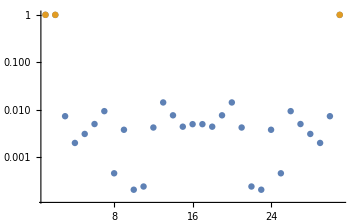
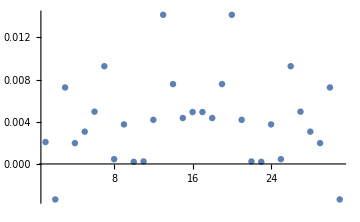
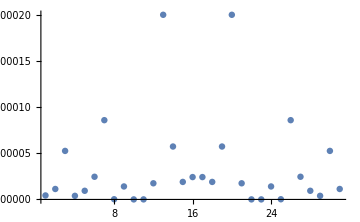
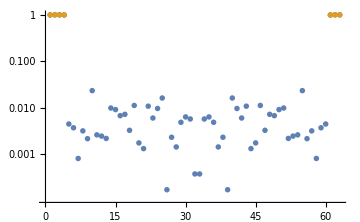
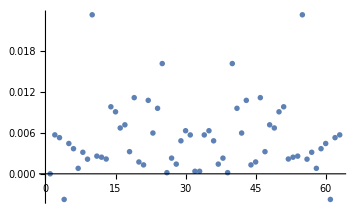
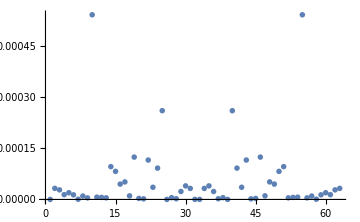
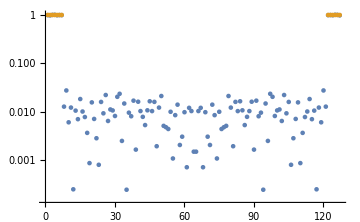
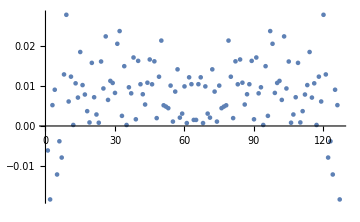
(0.1 | 5 | -Graphics- | -Graphics- | -Graphics- | 0.00104495 | 3.
0.1 | 6 | -Graphics- | -Graphics- | -Graphics- | 0.00340623 | 7.
0.1 | 7 | -Graphics- | -Graphics- | -Graphics- | 0.0165431 | 13.
0.1 | 8 | -Graphics- | -Graphics- | -Graphics- | 0.0488333 | 25.
0.1 | 9 | -Graphics- | -Graphics- | -Graphics- | 0.263247 | 51.
0.1 | 10 | -Graphics- | -Graphics- | -Graphics- | 0.862274 | 103.)

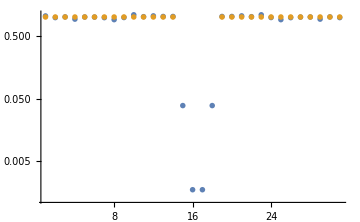
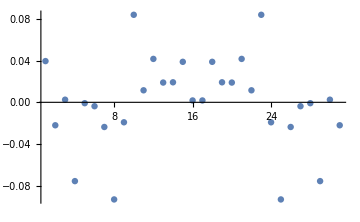
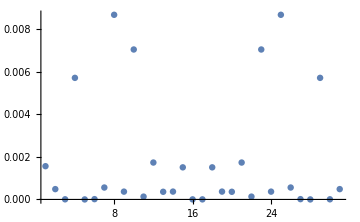
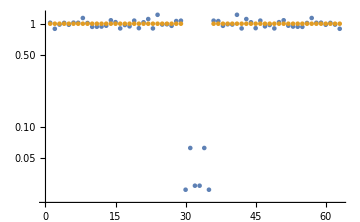
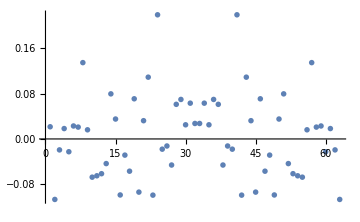
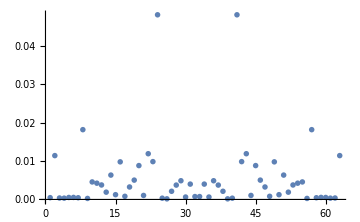
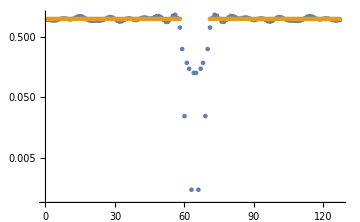
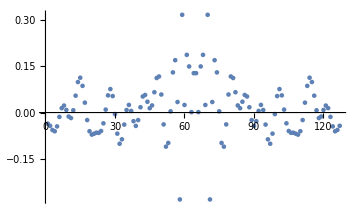
(0.9 | 5 | -Graphics- | -Graphics- | -Graphics- | 0.0555405 | 27.
0.9 | 6 | -Graphics- | -Graphics- | -Graphics- | 0.338522 | 57.
0.9 | 7 | -Graphics- | -Graphics- | -Graphics- | 0.959784 | 115.
0.9 | 8 | -Graphics- | -Graphics- | -Graphics- | 2.0203 | 229.
0.9 | 9 | -Graphics- | -Graphics- | -Graphics- | 4.08828 | 459.
0.9 | 10 | -Graphics- | -Graphics- | -Graphics- | 8.1669 | 921.)

```mathematica
CalcErrors[0.1,3]//MatrixForm
CalcErrors[0.9,3]//MatrixForm
```

```mathematica
CleanCalc[part_,bit_]:=
{#[[1]][[1]],#[[2]][[1]],#[[3]][[1]]}&/@CalcErrors[part,bit]
```

```mathematica
NotebookDirectory[]
```

/Users/masteranza/Dropbox/Knowledge/Science/Information/Processing/Filters/firWindowing/

```mathematica
AppendTo[$Path,NotebookDirectory[]];
```

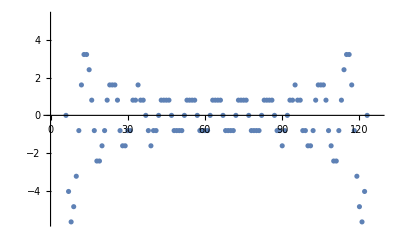

```mathematica
names=Outer["filtr"<>ToString[#1-1]<>"-"<>ToString[#2]<>".dat" &,nn,bits];
names2=Outer["filtr"<>ToString[#1-1]<>"-64.dat" &,nn];
data=Map[Import[#,"Data"][[All,11]]&,names,{2}];
ListPlot[data[[3,3]]]
(*dplots=Map[Import[#,"Data"][[All,7]]&,names,{2}];*)
dataDouble=Map[Import[#,"Data"][[All,13]]&,names2];
trans=Map[Import[#,"Data"][[All,1]]&,names,{2}];
transref=Map[Import[#,"Data"][[All,13]]&,names,{2}];

(*ListLinePlot[{trans[[4,8]],transref[[4,8]]},PlotRange->Full,ImageSize->Large];*)
rotData=Map[RotateLeft[#,(Length@#+1)/2]&,data,{2}];
data2=Map[Abs@Fourier[#, FourierParameters->{-1, 1}]&,data,{2}];
rotData2=Map[Abs@Fourier[#, FourierParameters->{-1, 1}]&,rotData,{2}];
(*dataPlot2=Map[ListLogPlot[#,PlotRange->Full,Joined->True,ImageSize->450]&,data2,{2}];*)
(*dataPlot=Map[ListLogPlot[Abs@#,PlotRange->Full,Joined->True,ImageSize->450]&,data,{2}];*)
(*Grid@Prepend[dataPlot,bits];*)

DTFT=Map[ListFourierSequenceTransform[#,x]/Length@(#)&,data,{2}];
rotDTFT=Map[ListFourierSequenceTransform[#,x]/Length@#&,rotData,{2}];
```

```mathematica
Table[{len+4,Total[Abs[(Abs@data2[[len,5]]-dataDouble[[len]])]]/(2^(len+4))},{len,1,Length@DTFT}]
```

{{5,0.000884525},{6,0.00124369},{7,0.00149339},{8,0.00192144},{9,0.00271577},{10,0.00290028}}

```mathematica
Table[{len+4,RootMeanSquare[(Abs@data2[[len,5]]-dataDouble[[len]])]},{len,1,Length@DTFT}]
```

{{5,0.00125954},{6,0.00174454},{7,0.00230677},{8,0.00333029},{9,0.00507806},{10,0.00643835}}

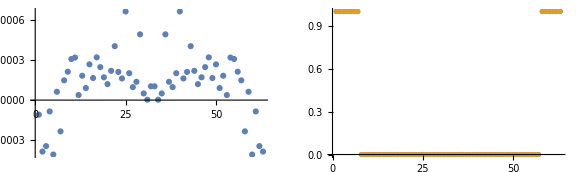

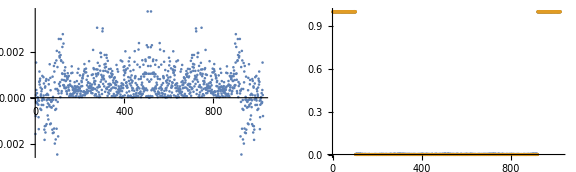

```mathematica
bitts=6;
wspol={2,6};
GraphicsRow[{ListPlot[data2[[wspol[[1]],bitts]]-dataDouble[[wspol[[1]]]],PlotRange->Full],ListPlot[{data2[[wspol[[1]],bitts]],dataDouble[[wspol[[1]]]]},PlotRange->Full]},ImageSize->Large]
GraphicsRow[{ListPlot[data2[[wspol[[2]],bitts]]-dataDouble[[wspol[[2]]]],PlotRange->Full],ListPlot[{data2[[wspol[[2]],bitts]],dataDouble[[wspol[[2]]]]},PlotRange->Full]},ImageSize->Large]
```

```mathematica
data[[2]]
```

```mathematica
wsp=1;
bit=4;
(*zdyskretyzowane współczynniki filtru*)
dataWsp=Map[Import[#,"Data"][[All,11]]&,names,{2}];
(*wartość bezwględna transmitancji z programu afilters*)
dataMag=Map[Import[#,"Data"][[All,7]]&,names,{2}];
```

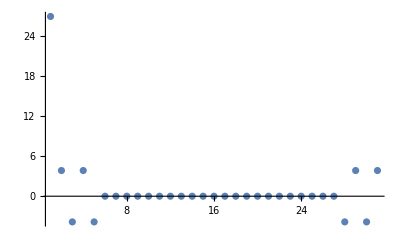

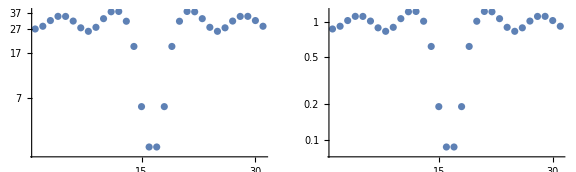

```mathematica
ListPlot[dataWsp[[wsp,bit]],PlotRange->Full]
GraphicsRow[{ListLogPlot[dataMag[[wsp,bit]],PlotRange->Full],
ListLogPlot[Abs@Fourier[dataWsp[[wsp,bit]], FourierParameters->{-1, 1}],PlotRange->Full]},ImageSize->Large]
```

me

{8,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1}

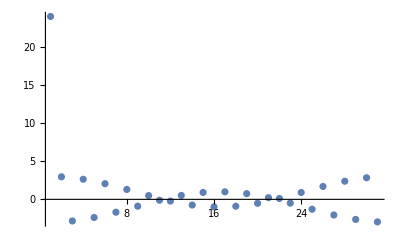

{27.,3.85714,-3.59296,3.11742,-2.48337,1.84932,-1.10959,0.422701,0.105675,-0.581213,0.898239,-1.05675,1.00391,-0.845401,0.528376,-0.158513,-0.158513,0.528376,-0.845401,1.00391,-1.05675,0.898239,-0.581213,0.105675,0.422701,-1.10959,1.84932,-2.48337,3.11742,-3.59296,3.85714}

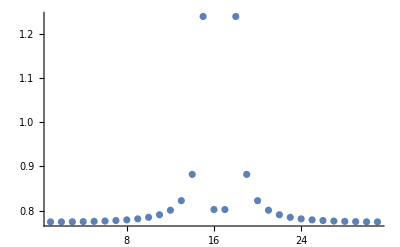

```mathematica
listaa=Flatten[Join[{8},Table[{1,-1},{i,1,Length@org/2}]]]
ListPlot[org  listaa,PlotRange->Full]
przes
ListPlot[Abs@Fourier[org  listaa[[1;;All]], FourierParameters->{-1, 1}],PlotRange->Full]
```

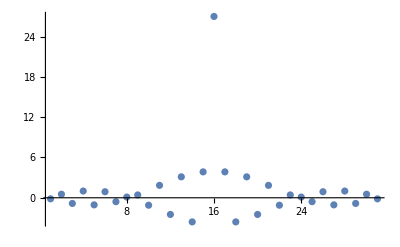

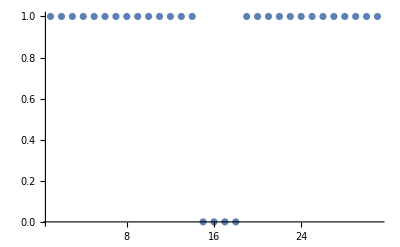

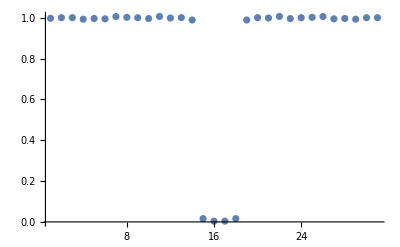

```mathematica
names=Outer["filtr"<>ToString[#1-1]<>"-"<>ToString[#2]<>".dat" &,nn,bits];
data=Map[Import[#,"Data"][[All,11]]&,names,{2}];
przes=RotateLeft[data[[wsp,bitt]],16];
l933=ListPlot[przes,PlotRange->Full]
trans=Map[Import[#,"Data"][[All,1]]&,names,{2}];
ListPlot[trans[[wsp,bitt]],PlotRange->Full]
ListPlot[Abs@Fourier[przes, FourierParameters->{-1, 1}],PlotRange->Full]
```

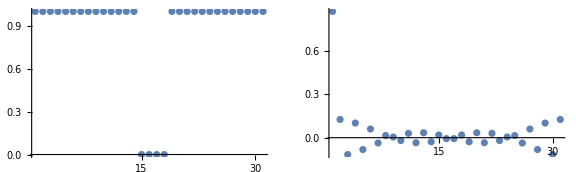

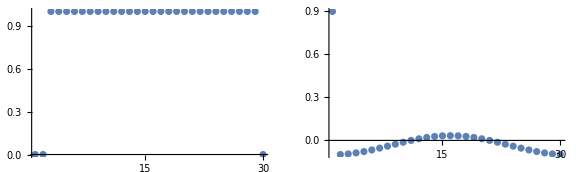

```mathematica
GraphicsRow[{ListPlot[trans[[wsp,bitt]],PlotRange->Full],ListPlot[Fourier[trans[[wsp,bitt]], FourierParameters->{-1, 1}],PlotRange->Full]},ImageSize->Large]
GraphicsRow[{ListPlot[Most@RotateRight[trans[[wsp,bitt]],15],PlotRange->Full],ListPlot[Chop@Fourier[Most@RotateRight[trans[[wsp,bitt]],15], FourierParameters->{-1, 1}],PlotRange->Full]},ImageSize->Large]
```

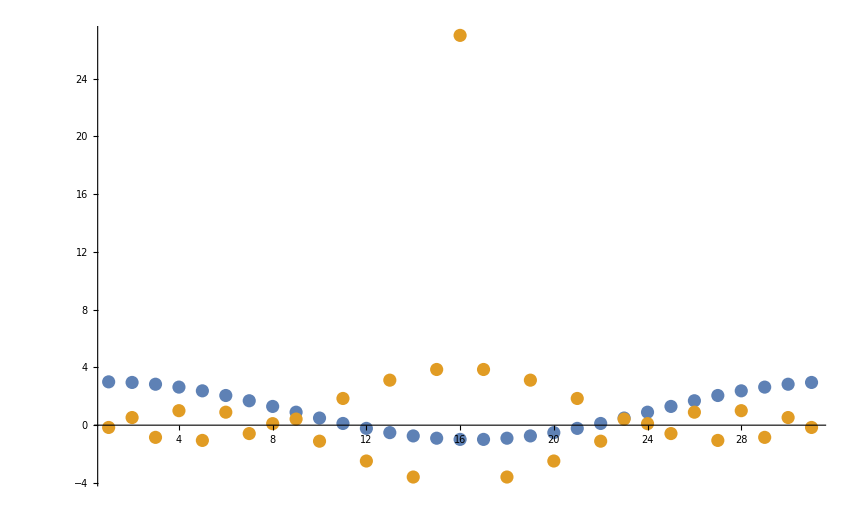

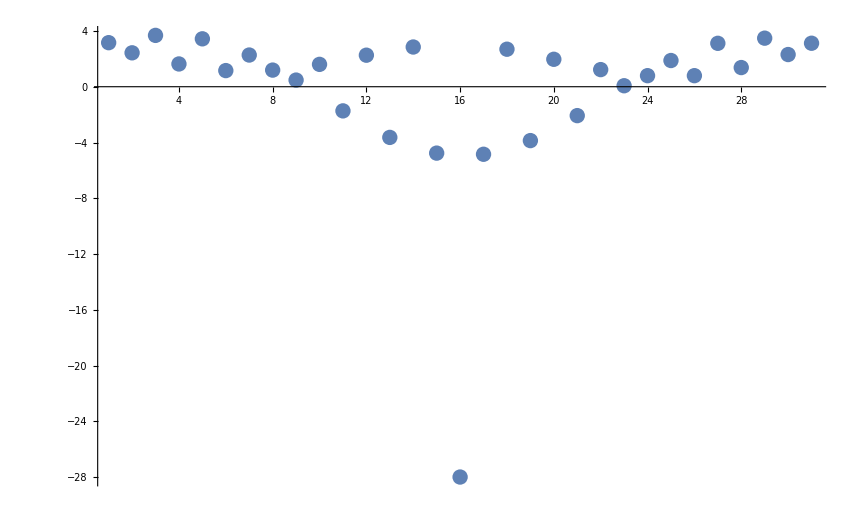

```mathematica
ListPlot[{org,przes},PlotRange->Full]
ListPlot[org-przes,PlotRange->Full]
```

```mathematica
bit=5;
wyniki=Flatten[Table[N@CalcErrors[widt,bit],{widt,0.1,0.9,0.1}],1];
ListContourPlot[wyniki,PlotLegends->Automatic,FrameLabel->{"Filter width","log_2[Filter Length]"},PlotLabel->"For "<>ToString[bit*2]<>" bits"]
```

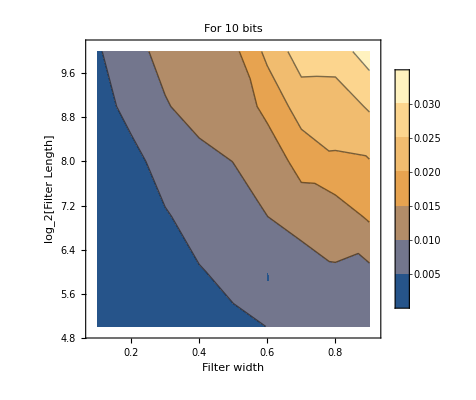

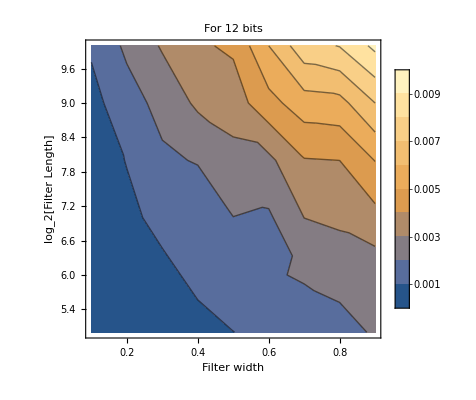

```mathematica
bit=6;
wyniki=Flatten[Table[N@CalcErrors[widt,bit],{widt,0.1,0.9,0.1}],1];
ListContourPlot[wyniki,PlotLegends->Automatic,FrameLabel->{"Filter width","log_2[Filter Length]"},PlotLabel->"For "<>ToString[bit*2]<>" bits"]
```

### Disc

```mathematica
bit=2;
wyniki=Flatten[Table[N@CalcErrors[widt,bit],{widt,0.1,0.9,0.1}],1];
ListContourPlot[wyniki,PlotLegends->Automatic,LabelStyle->Directive[Bold],FrameLabel->{"Filter width","log_2[Filter Length]"},PlotLabel->"For "<>ToString[bit*2]<>" bits"]
```

$Aborted

ListContourPlot[wyniki,PlotLegends→Automatic,LabelStyle→Directive[Bold],FrameLabel→{Filter width,log_2[Filter Length]},PlotLabel→For 4 bits]

```mathematica
wyniki2=Flatten[Table[N@CalcErrors[0.25,bit],{bit,2,32}],1];
```

```mathematica
dlu=Flatten@{Range[2,32],Range[2,32],Range[2,32],Range[2,32],Range[2,32],Range[2,32]}
```

{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32}

```mathematica
wyniki3=MapThread[{2#1,#2[[2]],#2[[3]]}&,{dlu,wyniki2},1];
```

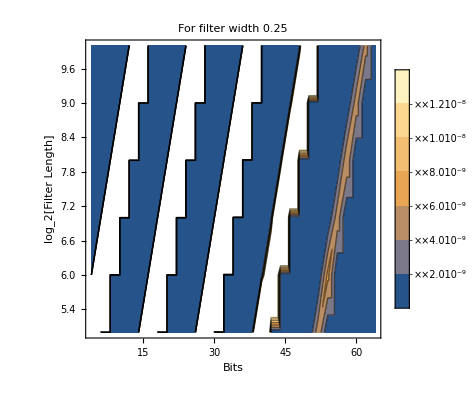

```mathematica
ListContourPlot[wyniki3,PlotLegends->Automatic,LabelStyle->Directive[Bold],FrameLabel->{"Bits","log_2[Filter Length]"},PlotLabel->"For filter width 0.25"]
```

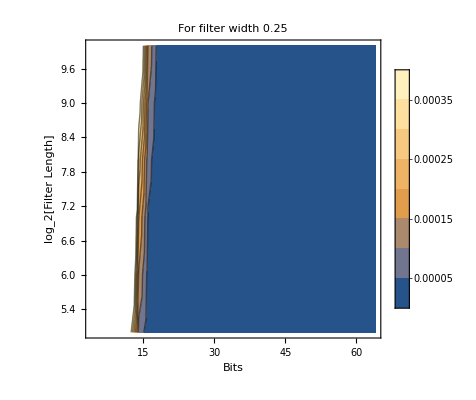

```mathematica
wyniki4=Flatten[Table[N@CalcErrors[0.25,bit],{bit,2,32}],1];
ListContourPlot[wyniki4,PlotLegends->Automatic,LabelStyle->Directive[Bold],FrameLabel->{"Bits","log_2[Filter Length]"},PlotLabel->"For filter width 0.25"]
```

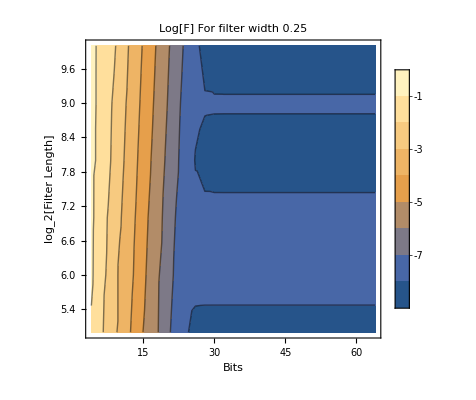

```mathematica
wyniki5={#[[1]],#[[2]],Log@Sqrt[#[[3]]]}&/@wyniki4;
ListContourPlot[wyniki5,PlotLegends->Automatic,LabelStyle->Directive[Bold],FrameLabel->{"Bits","log_2[Filter Length]"},PlotLabel->"Log[F] For filter width 0.25"]
```

```mathematica
Series[Tanh[x],{x,0,5}]
```

x-x^3/3+(2 x^5)/15+O[x]^6

### Miara ciągła

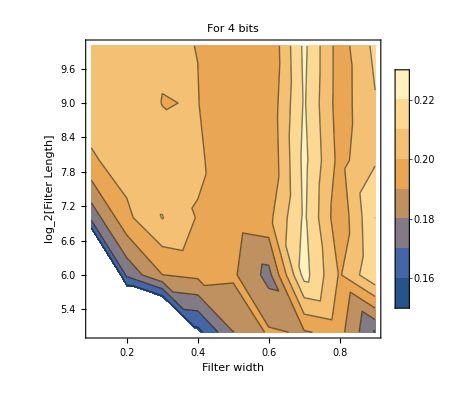

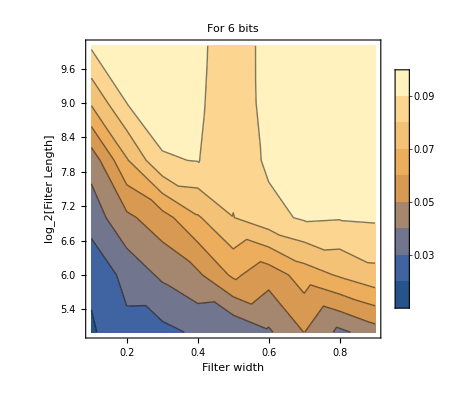

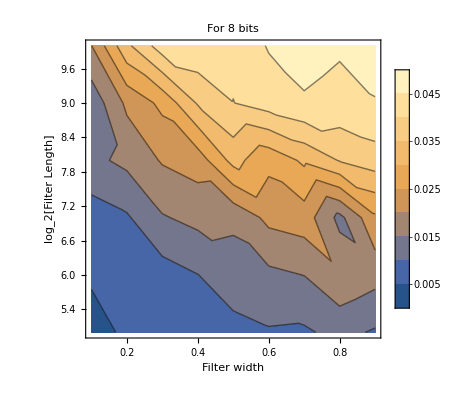

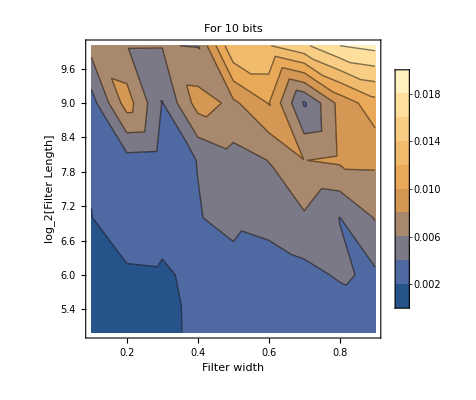

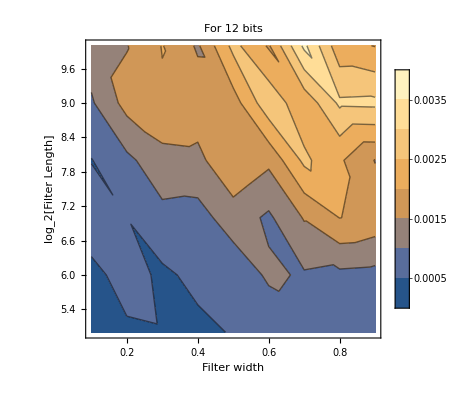

```mathematica
bit=2;
wyniki=Flatten[Table[N@CalcErrors[widt,bit],{widt,0.1,0.9,0.1}],1];
ListContourPlot[wyniki,PlotLegends->Automatic,LabelStyle->Directive[Bold],FrameLabel->{"Filter width","log_2[Filter Length]"},PlotLabel->"For "<>ToString[bit*2]<>" bits"]
bit=3;
wyniki=Flatten[Table[N@CalcErrors[widt,bit],{widt,0.1,0.9,0.1}],1];
ListContourPlot[wyniki,PlotLegends->Automatic,LabelStyle->Directive[Bold],FrameLabel->{"Filter width","log_2[Filter Length]"},PlotLabel->"For "<>ToString[bit*2]<>" bits"]
bit=4;
wyniki=Flatten[Table[N@CalcErrors[widt,bit],{widt,0.1,0.9,0.1}],1];
ListContourPlot[wyniki,PlotLegends->Automatic,LabelStyle->Directive[Bold],FrameLabel->{"Filter width","log_2[Filter Length]"},PlotLabel->"For "<>ToString[bit*2]<>" bits"]
bit=5;
wyniki=Flatten[Table[N@CalcErrors[widt,bit],{widt,0.1,0.9,0.1}],1];
ListContourPlot[wyniki,PlotLegends->Automatic,LabelStyle->Directive[Bold],FrameLabel->{"Filter width","log_2[Filter Length]"},PlotLabel->"For "<>ToString[bit*2]<>" bits"]
bit=6;
wyniki=Flatten[Table[N@CalcErrors[widt,bit],{widt,0.1,0.9,0.1}],1];
ListContourPlot[wyniki,PlotLegends->Automatic,LabelStyle->Directive[Bold],FrameLabel->{"Filter width","log_2[Filter Length]"},PlotLabel->"For "<>ToString[bit*2]<>" bits"]
```

Oznaczmy spektrum filtru idealnego o szerokości w przez T(w), a przez T_N(w) filtr uzyskany przy zapisie na N bitach. Wtedy mamy nasza miara wyraża się przez:

(∑(T_N(w)-T(w))^2)/(∑(T(w))^2)=1+(∑((T_N(w))^2-2T_N(w)T(w)))/(∑(T(w))^2)

```mathematica
a1=Reverse[Table[HeavisideTheta[(i-9.9)],{i,0,10,0.04}]]
a9=Reverse[Table[HeavisideTheta[(i-0.1)],{i,0,10,0.04}]]
rr=Table[0.01RandomReal[],{i,0,10,0.04}];
Total[rr^2]/Total[a1^2]
Total[rr^2]/Total[a9^2]
rr=-rr;
1+Total[(rr+a1)^2-2 (a1+rr)*a1]/Total[a1^2]
1+Total[(rr+a9)^2-2 (a9+rr)*a9]/Total[a9^2]
```

{1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0}

251

0.00253233

0.000030633

0.00253233

0.000030633

### Miara dyskretna

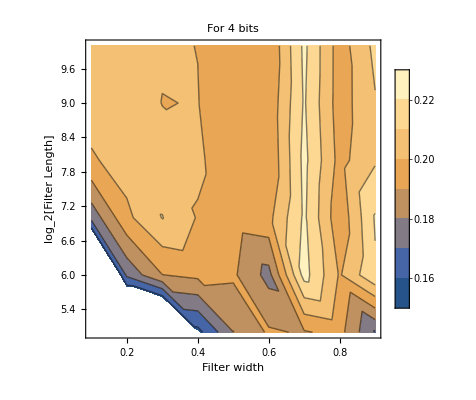

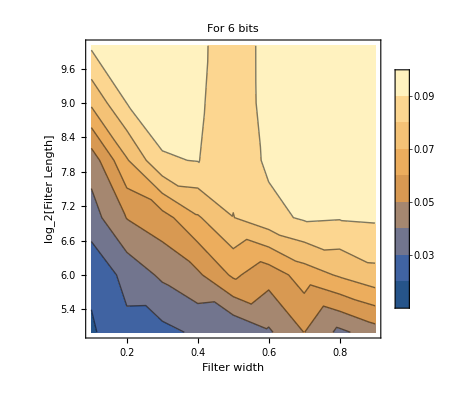

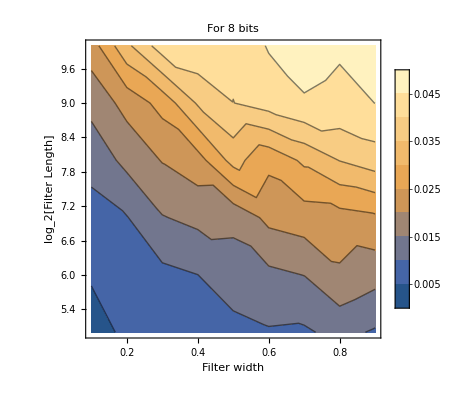

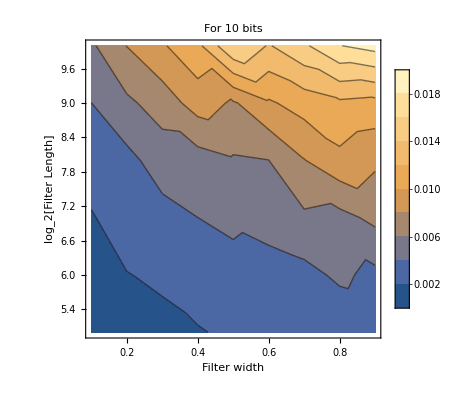

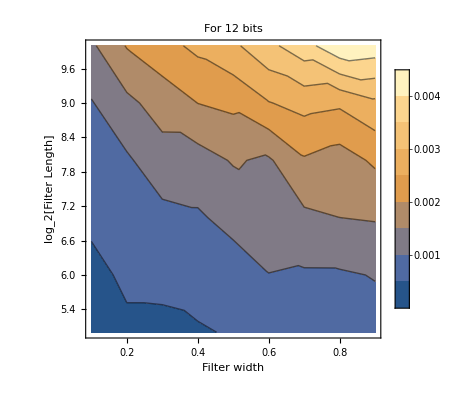

```mathematica
bit=2;
wyniki=Flatten[Table[N@CalcErrors[widt,bit],{widt,0.1,0.9,0.1}],1];
ListContourPlot[wyniki,PlotLegends->Automatic,LabelStyle->Directive[Bold],FrameLabel->{"Filter width","log_2[Filter Length]"},PlotLabel->"For "<>ToString[bit*2]<>" bits"]
bit=3;
wyniki=Flatten[Table[N@CalcErrors[widt,bit],{widt,0.1,0.9,0.1}],1];
ListContourPlot[wyniki,PlotLegends->Automatic,LabelStyle->Directive[Bold],FrameLabel->{"Filter width","log_2[Filter Length]"},PlotLabel->"For "<>ToString[bit*2]<>" bits"]
bit=4;
wyniki=Flatten[Table[N@CalcErrors[widt,bit],{widt,0.1,0.9,0.1}],1];
ListContourPlot[wyniki,PlotLegends->Automatic,LabelStyle->Directive[Bold],FrameLabel->{"Filter width","log_2[Filter Length]"},PlotLabel->"For "<>ToString[bit*2]<>" bits"]
bit=5;
wyniki=Flatten[Table[N@CalcErrors[widt,bit],{widt,0.1,0.9,0.1}],1];
ListContourPlot[wyniki,PlotLegends->Automatic,LabelStyle->Directive[Bold],FrameLabel->{"Filter width","log_2[Filter Length]"},PlotLabel->"For "<>ToString[bit*2]<>" bits"]
bit=6;
wyniki=Flatten[Table[N@CalcErrors[widt,bit],{widt,0.1,0.9,0.1}],1];
ListContourPlot[wyniki,PlotLegends->Automatic,LabelStyle->Directive[Bold],FrameLabel->{"Filter width","log_2[Filter Length]"},PlotLabel->"For "<>ToString[bit*2]<>" bits"]
```

```mathematica
len=1;
disc1=Table[Total[Abs[(Abs@data2[[len,j]]-dataDouble[[len]])]]/(2^(len+4)),{j,1,Length@DTFT[[1]]}];
len=4;
disc2=Table[Total[Abs[(Abs@data2[[len,j]]-dataDouble[[len]])]]/(2^(len+4)),{j,1,Length@DTFT[[1]]}];
len=6;
disc3=Table[Total[Abs[(Abs@data2[[len,j]]-dataDouble[[len]])]]/(2^(len+4)),{j,1,Length@DTFT[[1]]}];
```

```mathematica
len=1;
idDTFT1=
Table[NIntegrate[Abs@(DTFT[[len,j]]-perfectDTFT[[len]]),{x,0,π}],{j,1,Length@DTFT[[1]]}]
```

{0.560862,0.0883961,0.0142232,0.00456781,0.00125784,0.000319768,0.0000840061,0.0000210566,4.94192×10^-6,1.16956×10^-6,4.11186×10^-7,1.65989×10^-7,1.30003×10^-7,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
len=4;
idDTFT2=
Table[NIntegrate[Abs@(DTFT[[len,j]]-perfectDTFT[[len]]),{x,0,π}],{j,1,Length@DTFT[[1]]}]
```

{0.564402,0.121466,0.0461593,0.0124175,0.00326525,0.000779943,0.000184345,0.000049211,0.0000130107,3.31738×10^-6,7.95032×10^-7,1.9656×10^-7,6.66836×10^-8,3.91155×10^-8,2.48899×10^-8,1.31148×10^-18,1.31148×10^-18,1.31148×10^-18,1.31148×10^-18,1.31148×10^-18,1.31148×10^-18,1.31148×10^-18,1.31148×10^-18,1.31148×10^-18,1.31148×10^-18,1.31148×10^-18,1.31148×10^-18,1.31148×10^-18,NIntegrate[Abs[DTFT⟦len,j⟧-perfectDTFT⟦len⟧],{x,0,π}],0.,0.,0.}

```mathematica
len=6;
idDTFT1=
Table[NIntegrate[Abs@(DTFT[[len,j]]-perfectDTFT[[len]]),{x,0,π}],{j,1,Length@DTFT[[1]]}]
```

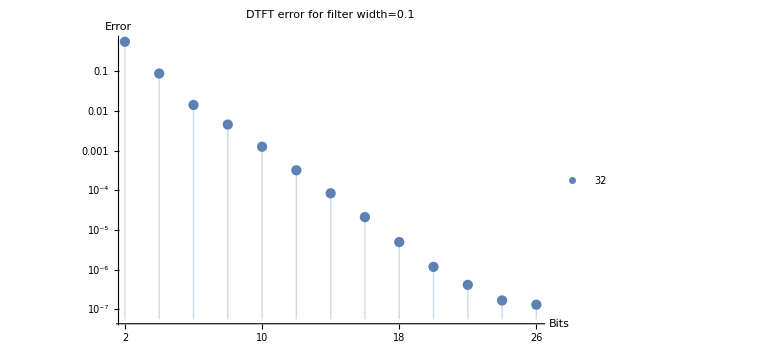

```mathematica
start=1;

listpoint = ListLogPlot[{idDTFT1[[start;;All]]},Filling->Bottom,DataRange->{start*2,Last@bits},PlotRange->Full, Ticks->{Range[start*2,Last@bits,2],Automatic},AxesLabel->{"Bits","Error"},ImageSize->Large,PlotLabel->("DTFT error for filter width=" <>ToString[part]), PlotLegends->{"32","256","1024"}]
```

```mathematica
Chop[21 +0.0000000001ⅈ]
```

21.+1.×10^-10 ⅈ

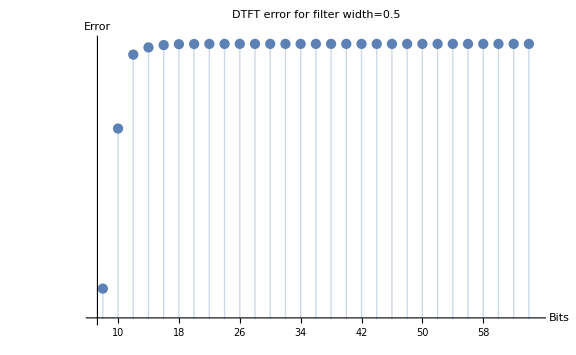

```mathematica
start=1;

listpoint = ListLogPlot[idrotDTFTMeanSq[[start;;All]],Filling->Bottom,DataRange->{start*2,Last@bits},PlotRange-> {{7,65},{1.94,1.9513}}, Ticks->{Range[start*2,Last@bits,2],Automatic},AxesLabel->{"Bits","Error"},ImageSize->Large,PlotLabel->("DTFT error for filter width=" <>ToString[part])]
```

### Part 0.1 Offset 0.5

```mathematica
RunWithPartLow[part_:0.4]:=Module[{transPlots,trans,transref,disc,dplots,start,names,data,rotData,data2,rotData2,dataPlot,dataPlot2,DTFT,rotDTFT,names2,dataDouble,data2Double,dataForInterLog,dataForInterDouble,interdDouble,idrotDTFTMeanSq,logDTFTs,listpoint,listpointd},
Run[OpenRead["!cd '/Users/masteranza/Dropbox/Knowledge/Science/Information/Processing/Filters/firWindowing/'; gcc -g -lm afilters.c kiss_fft.c kiss_fftr.c -o afilters; ./afilters "<>ToString[part]<>";"]];
Pause[15];
(*nn={32,64};
bits=Range[0,16,8];*)
names=Outer["filtr"<>ToString[#1-1]<>"-"<>ToString[#2]<>".dat" &,nn,bits];
data=Map[Import[#,"Data"][[All,11]]&,names,{2}];
(*dplots=Map[Import[#,"Data"][[All,7]]&,names,{2}];*)

trans=Map[Import[#,"Data"][[All,1]]&,names,{2}];
transref=Map[Import[#,"Data"][[All,13]]&,names,{2}];
transPlots=ListPlot[{trans[[1]][[1]],1+transref[[1]][[1]]},PlotRange->Full,Joined->False,ImageSize->450,PlotLabel->"Input - rozsunięte dla czytelności",PlotLegends->{"Transmittance","Ref Transmittance"}];
Export["/Users/masteranza/Dropbox/Knowledge/Science/Information/Processing/Filters/firWindowing/calculated/example-lowpass-part"<>ToString[part]<>".png",transPlots];

ListLinePlot[{trans[[4,8]],transref[[4,8]]},PlotRange->Full,ImageSize->Large];

rotData=Map[RotateLeft[#,(Length@#+1)/2]&,data,{2}];

data2=Map[Abs@Fourier[#, FourierParameters->{-1, 1}]&,data,{2}];
rotData2=Map[Abs@Fourier[#, FourierParameters->{-1, 1}]&,rotData,{2}];
dataPlot2=Map[ListLogPlot[#,PlotRange->Full,Joined->True,ImageSize->450]&,data2,{2}];
dataPlot=Map[ListLogPlot[Abs@#,PlotRange->Full,Joined->True,ImageSize->450]&,data,{2}];
Grid@Prepend[dataPlot,bits];

DTFT=Map[ListFourierSequenceTransform[#,x]/Length@(#)&,data,{2}];
rotDTFT=Map[ListFourierSequenceTransform[#,x]/Length@#&,rotData,{2}];
dataForInterLog= Map[{Table[i,{i,0,1-1/(Length@#),2/(Length@#)}]π,Log@#[[1;;(Length@#+1)/2]]}ᵀ &,data2,{2}];

names2=Outer["filtr"<>ToString[#1-1]<>"-64.dat" &,nn];
dataDouble=Map[Import[#,"Data"][[All,13]]&,names2];
(*data2Double=Map[Abs@Fourier[#, FourierParameters->{-1, 1}]&,dataDouble,{1}];*)
dataForInterDouble= Map[{Table[i,{i,0,1-1/(Length@#),2/(Length@#)}]π,#[[1;;(Length@#+1)/2]]}ᵀ &,dataDouble];
interdDouble=Table[Interpolation[dataForInterDouble[[i]],InterpolationOrder->0][x],{i,1,Length@DTFT}];
idrotDTFTMeanSq =Table[NIntegrate[Abs@(rotDTFT[[i,j]]-interdDouble[[i]]),{x,0,π}],{i,1,Length@DTFT},{j,1,Length@DTFT[[1]]}];

start=4;

listpoint = ListLinePlot[idrotDTFTMeanSq[[1,start;;All]],Filling->Bottom,DataRange->{start*2,Last@bits},PlotRange->Full,Ticks->{Range[start*2,Last@bits,2],Automatic},AxesLabel->{"Bits","Error"},ImageSize->Large,PlotLabel->("DTFT error for filter width=" <>ToString[part])];

Export ["/Users/masteranza/Dropbox/Knowledge/Science/Information/Processing/Filters/firWindowing/calculated/lowpass-point-part-32"<>ToString[part]<>".png",listpoint]

 disc=Table[Total[Abs[(Abs@data2[[i,j]]-dataDouble[[i]])]]/(2^(i+4)),{i,1,Length@DTFT},{j,1,Length@DTFT[[1]]}];
listpointd = ListPointPlot3D[disc[[1;;All,start;;All]]ᵀ,Filling->Bottom,PlotStyle->PointSize[Large],DataRange->{{5,10},{start*2,16}},PlotRange->Full,FillingStyle->Directive[Red,Dashed, Thick],Ticks->{Range[2,10,1],Range[start*2,16,2],Automatic},AxesLabel->{"Log[Length]","Bits","Error"},ImageSize->Large,PlotLabel->("Discrete error for filter width=" <>ToString[part])];

logDTFTs=Table[leeg[{(Abs@rotDTFT[[i,j]])},{x,0,π},dataForInterLog[[i,j]],{idrotDTFTMeanSq[[i,j]]},{"rotCoefs"},PlotRange->All,ImageSize->450],{i,1,Length@DTFT},{j,1,Length@DTFT[[1]]}];

Export["/Users/masteranza/Dropbox/Knowledge/Science/Information/Processing/Filters/firWindowing/calculated/plots-lowpass-part"<>ToString[part]<>".png",Grid@Prepend[logDTFTs,bits]];

Export ["/Users/masteranza/Dropbox/Knowledge/Science/Information/Processing/Filters/firWindowing/calculated/lowpass-part"<>ToString[part]<>".png",TemperatureGrid[idrotDTFTMeanSq[[1;;All,start;;All]],bits[[start;;All]]]];

Export ["/Users/masteranza/Dropbox/Knowledge/Science/Information/Processing/Filters/firWindowing/calculated/lowpass-discrete-part"<>ToString[part]<>".png",TemperatureGrid[disc[[1;;All,start;;All]],bits[[start;;All]]]];

(*Export ["/Users/masteranza/Dropbox/Knowledge/Science/Information/Processing/Filters/firWindowing/calculated/lowpass-point-part"<>ToString[part]<>".png",listpoint];
Export ["/Users/masteranza/Dropbox/Knowledge/Science/Information/Processing/Filters/firWindowing/calculated/lowpass-pointd-part"<>ToString[part]<>".png",listpointd];*)

TemperatureGrid[idrotDTFTMeanSq]
];
```

```mathematica
RunWithPartLow[0.1]
RunWithPartLow[0.2]
RunWithPartLow[0.4]
```

| 2 | 4 | 6 | 8 | 10 | 12 | 14 | 16
32 | 0.486932 | 0.449707 | 0.464872 | 0.469239 | 0.472056 | 0.472608 | 0.47272 | 0.47275
64 | 0.615425 | 0.498366 | 0.479962 | 0.486793 | 0.489934 | 0.490872 | 0.49099 | 0.491036
128 | 0.589063 | 0.463046 | 0.445499 | 0.43792 | 0.439829 | 0.440735 | 0.440883 | 0.440947
256 | 0.575518 | 0.449774 | 0.42406 | 0.409921 | 0.409102 | 0.409479 | 0.40968 | 0.409735
512 | 0.590969 | 0.45867 | 0.428918 | 0.411463 | 0.406972 | 0.407339 | 0.407527 | 0.407585
1024 | 0.598773 | 0.467397 | 0.432061 | 0.416532 | 0.408674 | 0.407225 | 0.407259 | 0.407308

| 2 | 4 | 6 | 8 | 10 | 12 | 14 | 16
32 | 1.18366 | 0.968369 | 0.941609 | 0.955924 | 0.958445 | 0.959481 | 0.959857 | 0.959969
64 | 1.13163 | 0.881835 | 0.872213 | 0.8759 | 0.879035 | 0.879838 | 0.880128 | 0.880203
128 | 1.10196 | 0.854461 | 0.829171 | 0.813478 | 0.817258 | 0.818258 | 0.818451 | 0.818523
256 | 1.12684 | 0.867583 | 0.833066 | 0.811714 | 0.810361 | 0.811721 | 0.811972 | 0.812098
512 | 1.14008 | 0.877417 | 0.848703 | 0.822771 | 0.813078 | 0.812647 | 0.812942 | 0.813038
1024 | 1.13691 | 0.875642 | 0.838162 | 0.818017 | 0.808738 | 0.806817 | 0.806754 | 0.806834

| 2 | 4 | 6 | 8 | 10 | 12 | 14 | 16
32 | 2.09478 | 1.74222 | 1.73677 | 1.76425 | 1.77502 | 1.77587 | 1.77664 | 1.77674
64 | 2.02386 | 1.66919 | 1.63515 | 1.63759 | 1.64108 | 1.64384 | 1.64439 | 1.64457
128 | 2.04877 | 1.6806 | 1.64461 | 1.61748 | 1.61655 | 1.61797 | 1.61852 | 1.6187
256 | 2.06811 | 1.69809 | 1.65794 | 1.62724 | 1.62168 | 1.62268 | 1.62309 | 1.62321
512 | 2.06334 | 1.69501 | 1.65987 | 1.62368 | 1.61537 | 1.61444 | 1.61463 | 1.61483
1024 | 2.05912 | 1.69098 | 1.6501 | 1.62473 | 1.60735 | 1.60496 | 1.60467 | 1.60477

### Part 0.2 Offset 0.5

```mathematica
nn={32,64,128,256,512,1024};
bits=Range[2,16,2];
(*nn={32,64};
bits=Range[0,16,8];*)
names=Outer["filtr"<>ToString[#1-1]<>"m-"<>ToString[#2]<>".dat" &,nn,bits];
data=Map[Import[#,"Data"][[All,11]]&,names,{2}];
rotData=Map[RotateLeft[#,(Length@#+1)/2]&,data,{2}];
```

```mathematica
data2=Map[Abs@Fourier[#, FourierParameters->{-1, 1}]&,data,{2}];
rotData2=Map[Abs@Fourier[#, FourierParameters->{-1, 1}]&,rotData,{2}];
dataPlot=Map[ListLogPlot[#,PlotRange->Full,Joined->True,ImageSize->450]&,data2,{2}];
dataPlot=Map[ListLogPlot[Abs@#,PlotRange->Full,Joined->True,ImageSize->450]&,data,{2}];
Grid@Prepend[dataPlot,bits];
```

```mathematica
DTFT=Map[ListFourierSequenceTransform[#,x]/Length@(#)&,data,{2}];
rotDTFT=Map[ListFourierSequenceTransform[#,x]/Length@#&,rotData,{2}];
```

```mathematica
names2=Outer["filtr"<>ToString[#1-1]<>"m-16.dat" &,nn];
dataDouble=Map[Import[#,"Data"][[All,9]]&,names2];
data2Double=Map[Abs@Fourier[#, FourierParameters->{-1, 1}]&,dataDouble,{1}];
dataForInterDouble= Map[{Table[i,{i,0,1-1/(Length@#),2/(Length@#)}]π,#[[1;;(Length@#+1)/2]]}ᵀ &,data2Double];
interdDouble=Table[Interpolation[dataForInterDouble[[i]],InterpolationOrder->0][x],{i,1,Length@DTFT}];
```

```mathematica
Total@(data2[[1,5]]-data2Double[[1]])
```

0.00701967

1

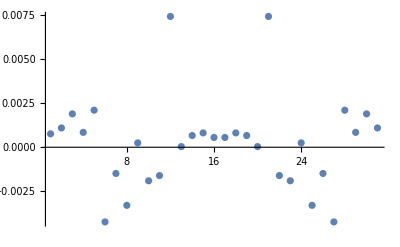

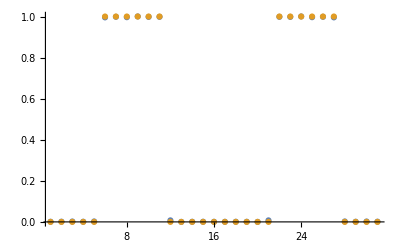

1024

```mathematica
cc=1
ListPlot[{data2[[cc,5]]-data2Double[[cc]]},PlotRange->Full]
ListPlot[{data2[[cc,5]],data2Double[[cc]]},PlotRange->Full]
```

```mathematica
start=4;
ttt= Table[Total[Abs[(Abs@data2[[i,j]]-data2Double[[i]])]]/(2^(i+4)),{i,1,Length@DTFT},{j,1,Length@DTFT[[1]]}];
TemperatureGrid@ttt
 ListPointPlot3D[ttt[[1;;All,start;;All]]ᵀ,Filling->Bottom,PlotStyle->PointSize[Large],DataRange->{{5,10},{start*2,16}},PlotRange->Full,FillingStyle->Directive[Red,Dashed, Thick],Ticks->{Range[2,10,1],Range[start*2,16,2],Automatic},AxesLabel->{"Log[Length]","Bits","Error"},ImageSize->Large]
TemperatureGrid@idrotDTFTMeanSq
ListPointPlot3D[idrotDTFTMeanSq[[1;;All,start;;All]]ᵀ,Filling->Bottom,PlotStyle->PointSize[Large],DataRange->{{5,10},{start*2,16}},PlotRange->Full,FillingStyle->Directive[Red,Dashed, Thick],Ticks->{Range[2,10,1],Range[start*2,16,2],Automatic},AxesLabel->{"Log[Length]","Bits","Error"},ImageSize->Large]
```

| 2 | 4 | 6 | 8 | 10 | 12 | 14 | 16
32 | 0.459677 | 0.13104 | 0.0248076 | 0.00580895 | 0.00178186 | 0.00043523 | 0.000101489 | 0.0000297868
64 | 0.477183 | 0.0890488 | 0.036593 | 0.010459 | 0.00264306 | 0.000713314 | 0.000171651 | 0.0000370682
128 | 0.473671 | 0.0961528 | 0.0437732 | 0.011244 | 0.00295483 | 0.000798042 | 0.000187484 | 0.0000464291
256 | 0.478125 | 0.0936195 | 0.0434702 | 0.0143263 | 0.00388356 | 0.000978708 | 0.000223458 | 0.0000545453
512 | 0.478749 | 0.094114 | 0.0444095 | 0.0169885 | 0.00428851 | 0.00132694 | 0.000344469 | 0.0000902784
1024 | 0.479843 | 0.0936133 | 0.0434811 | 0.016699 | 0.00567903 | 0.00169835 | 0.000487078 | 0.000116451

-Graphics3D-

| 2 | 4 | 6 | 8 | 10 | 12 | 14 | 16
32 | 0.745352 | 0.196442 | 0.151916 | 0.151365 | 0.154202 | 0.154327 | 0.154394 | 0.154413
64 | 0.761454 | 0.0738401 | 0.0624463 | 0.0707718 | 0.0762508 | 0.0776726 | 0.0780352 | 0.078091
128 | 0.7499 | 0.0797188 | 0.0238425 | 0.0324828 | 0.0362899 | 0.0377477 | 0.0380569 | 0.0381317
256 | 0.753982 | 0.0754174 | 0.0214395 | 0.0137352 | 0.0170702 | 0.0184384 | 0.0187462 | 0.0188389
512 | 0.753488 | 0.0760779 | 0.0216556 | 0.012436 | 0.00937509 | 0.00932734 | 0.00934193 | 0.00934577
1024 | 0.754472 | 0.0748306 | 0.0206863 | 0.00522873 | 0.00376806 | 0.00427277 | 0.00456295 | 0.00464792

-Graphics3D-

#### Odchylenie rotDTFT od idealnej ciągłej

```mathematica
idrotDTFTMeanSq =Table[NIntegrate[(Abs@rotDTFT[[i,j]]-interdDouble[[i]])^2,{x,0,π}],{i,1,Length@DTFT},{j,1,Length@DTFT[[1]]}];
TemperatureGrid[idrotDTFTMeanSq]
```

| 2 | 4 | 6 | 8 | 10 | 12 | 14 | 16
32 | 0.745352 | 0.196442 | 0.151916 | 0.151365 | 0.154202 | 0.154327 | 0.154394 | 0.154413
64 | 0.761454 | 0.0738401 | 0.0624463 | 0.0707718 | 0.0762508 | 0.0776726 | 0.0780352 | 0.078091
128 | 0.7499 | 0.0797188 | 0.0238425 | 0.0324828 | 0.0362899 | 0.0377477 | 0.0380569 | 0.0381317
256 | 0.753982 | 0.0754174 | 0.0214395 | 0.0137352 | 0.0170702 | 0.0184384 | 0.0187462 | 0.0188389
512 | 0.753488 | 0.0760779 | 0.0216556 | 0.012436 | 0.00937509 | 0.00932734 | 0.00934193 | 0.00934577
1024 | 0.754472 | 0.0748306 | 0.0206863 | 0.00522873 | 0.00376806 | 0.00427277 | 0.00456295 | 0.00464792

```mathematica
logDTFTs=Table[leeg[{(Abs@rotDTFT[[i,j]])},{x,0,π},dataForInterLog[[i,j]],{idrotDTFTMeanSq[[i,j]]},{"rotCoefs"},PlotRange->All,ImageSize->450],{i,1,Length@DTFT},{j,1,Length@DTFT[[1]]}];
```

```mathematica
Export["/Users/masteranza/Dropbox/Knowledge/Science/Information/Processing/Filters/firWindowing/calculated/plots-midpass-part0.2offset0.5.png",Grid@Prepend[logDTFTs,bits]];
```

```mathematica
Export ["/Users/masteranza/Dropbox/Knowledge/Science/Information/Processing/Filters/firWindowing/calculated/midpass-part0.2offset0.5.png",TemperatureGrid[idrotDTFTMeanSq]];
```

### Part 0.3 Offset 0.5

```mathematica
nn={32,64,128,256,512,1024};
bits=Range[2,16,2];
(*nn={32,64};
bits=Range[0,16,8];*)
names=Outer["filtr"<>ToString[#1-1]<>"m-"<>ToString[#2]<>".dat" &,nn,bits];
data=Map[Import[#,"Data"][[All,11]]&,names,{2}];
rotData=Map[RotateLeft[#,(Length@#+1)/2]&,data,{2}];
```

```mathematica
data2=Map[Abs@Fourier[#, FourierParameters->{-1, 1}]&,data,{2}];
rotData2=Map[Abs@Fourier[#, FourierParameters->{-1, 1}]&,rotData,{2}];
dataPlot=Map[ListLogPlot[#,PlotRange->Full,Joined->True,ImageSize->450]&,data2,{2}];
dataPlot=Map[ListLogPlot[Abs@#,PlotRange->Full,Joined->True,ImageSize->450]&,data,{2}];
Grid@Prepend[dataPlot,bits];
```

```mathematica
DTFT=Map[ListFourierSequenceTransform[#,x]/Length@(#)&,data,{2}];
rotDTFT=Map[ListFourierSequenceTransform[#,x]/Length@#&,rotData,{2}];
```

```mathematica
dataForInter= Map[{Table[i,{i,0,1-1/(Length@#),2/(Length@#)}]π,#[[1;;(Length@#+1)/2]]}ᵀ &,data2,{2}];
dataForInterLog= Map[{Table[i,{i,0,1-1/(Length@#),2/(Length@#)}]π,Log@#[[1;;(Length@#+1)/2]]}ᵀ &,data2,{2}];
```

```mathematica
names2=Outer["filtr"<>ToString[#1-1]<>"m-16.dat" &,nn];
dataDouble=Map[Import[#,"Data"][[All,9]]&,names2];
data2Double=Map[Abs@Fourier[#, FourierParameters->{-1, 1}]&,dataDouble,{1}];
dataForInterDouble= Map[{Table[i,{i,0,1-1/(Length@#),2/(Length@#)}]π,#[[1;;(Length@#+1)/2]]}ᵀ &,data2Double];
interdDouble=Table[Interpolation[dataForInterDouble[[i]],InterpolationOrder->0][x],{i,1,Length@DTFT}];
```

#### Odchylenie rotDTFT od idealnej ciągłej

```mathematica
idrotDTFTMeanSq =Table[NIntegrate[(Abs@rotDTFT[[i,j]]-interdDouble[[i]])^2,{x,0,π}],{i,1,Length@DTFT},{j,1,Length@DTFT[[1]]}];
TemperatureGrid[idrotDTFTMeanSq]
```

| 2 | 4 | 6 | 8 | 10 | 12 | 14 | 16
32 | 0.745352 | 0.196442 | 0.151916 | 0.151365 | 0.154202 | 0.154327 | 0.154394 | 0.154413
64 | 0.761454 | 0.0738401 | 0.0624463 | 0.0707718 | 0.0762508 | 0.0776726 | 0.0780352 | 0.078091
128 | 0.7499 | 0.0797188 | 0.0238425 | 0.0324828 | 0.0362899 | 0.0377477 | 0.0380569 | 0.0381317
256 | 0.753982 | 0.0754174 | 0.0214395 | 0.0137352 | 0.0170702 | 0.0184384 | 0.0187462 | 0.0188389
512 | 0.753488 | 0.0760779 | 0.0216556 | 0.012436 | 0.00937509 | 0.00932734 | 0.00934193 | 0.00934577
1024 | 0.754472 | 0.0748306 | 0.0206863 | 0.00522873 | 0.00376806 | 0.00427277 | 0.00456295 | 0.00464792

4

-Graphics3D-

```mathematica
logDTFTs=Table[leeg[{(Abs@rotDTFT[[i,j]])},{x,0,π},dataForInterLog[[i,j]],{idrotDTFTMeanSq[[i,j]]},{"rotCoefs"},PlotRange->All,ImageSize->450],{i,1,Length@DTFT},{j,1,Length@DTFT[[1]]}];
```

```mathematica
Export["/Users/masteranza/Dropbox/Knowledge/Science/Information/Processing/Filters/firWindowing/calculated/plots-midpass-part0.3offset0.5.png",Grid@Prepend[logDTFTs,bits]];
```

```mathematica
Export ["/Users/masteranza/Dropbox/Knowledge/Science/Information/Processing/Filters/firWindowing/calculated/midpass-part0.3offset0.5.png",TemperatureGrid[idrotDTFTMeanSq]];
```

### Part 0.4 Offset 0.5

```mathematica
nn={32,64,128,256,512,1024};
bits=Range[2,16,2];
(*nn={32,64};
bits=Range[0,16,8];*)
names=Outer["filtr"<>ToString[#1-1]<>"m-"<>ToString[#2]<>".dat" &,nn,bits];
data=Map[Import[#,"Data"][[All,11]]&,names,{2}];
rotData=Map[RotateLeft[#,(Length@#+1)/2]&,data,{2}];
```

```mathematica
data2=Map[Abs@Fourier[#, FourierParameters->{-1, 1}]&,data,{2}];
rotData2=Map[Abs@Fourier[#, FourierParameters->{-1, 1}]&,rotData,{2}];
dataPlot=Map[ListLogPlot[#,PlotRange->Full,Joined->True,ImageSize->450]&,data2,{2}];
dataPlot=Map[ListLogPlot[Abs@#,PlotRange->Full,Joined->True,ImageSize->450]&,data,{2}];
Grid@Prepend[dataPlot,bits];
```

```mathematica
dataForInter= Map[{Table[i,{i,0,1-1/(Length@#),2/(Length@#)}]π,#[[1;;(Length@#+1)/2]]}ᵀ &,data2,{2}];
dataForInterLog= Map[{Table[i,{i,0,1-1/(Length@#),2/(Length@#)}]π,Log@#[[1;;(Length@#+1)/2]]}ᵀ &,data2,{2}];
```

```mathematica
DTFT=Map[ListFourierSequenceTransform[#,x]/Length@(#)&,data,{2}];
rotDTFT=Map[ListFourierSequenceTransform[#,x]/Length@#&,rotData,{2}];
```

```mathematica
names2=Outer["filtr"<>ToString[#1-1]<>"m-16.dat" &,nn];
dataDouble=Map[Import[#,"Data"][[All,9]]&,names2];
data2Double=Map[Abs@Fourier[#, FourierParameters->{-1, 1}]&,dataDouble,{1}];
dataForInterDouble= Map[{Table[i,{i,0,1-1/(Length@#),2/(Length@#)}]π,#[[1;;(Length@#+1)/2]]}ᵀ &,data2Double];
interdDouble=Table[Interpolation[dataForInterDouble[[i]],InterpolationOrder->0][x],{i,1,Length@DTFT}];
```

#### Odchylenie rotDTFT od idealnej ciągłej

```mathematica
idrotDTFTMeanSq =Table[NIntegrate[(Abs@rotDTFT[[i,j]]-interdDouble[[i]])^2,{x,0,π}],{i,1,Length@DTFT},{j,1,Length@DTFT[[1]]}];
TemperatureGrid[idrotDTFTMeanSq]
```

```mathematica
logDTFTs=Table[leeg[{(Abs@rotDTFT[[i,j]])},{x,0,π},dataForInterLog[[i,j]],{idrotDTFTMeanSq[[i,j]]},{"rotCoefs"},PlotRange->All,ImageSize->450],{i,1,Length@DTFT},{j,1,Length@DTFT[[1]]}];
```

```mathematica
Export["/Users/masteranza/Dropbox/Knowledge/Science/Information/Processing/Filters/firWindowing/calculated/plots-midpass-part0.4offset0.5.png",Grid@Prepend[logDTFTs,bits]];
```

```mathematica
Export ["/Users/masteranza/Dropbox/Knowledge/Science/Information/Processing/Filters/firWindowing/calculated/midpass-part0.4offset0.5.png",TemperatureGrid[idrotDTFTMeanSq]];
```

## Mid pass

### Part 0.1 Offset 0.5

```mathematica
RunWithPart[part_:0.4,offset_:0.5]:=Module[{names,data,rotData,data2,rotData2,dataPlot,DTFT,rotDTFT,names2,dataDouble,data2Double,dataForInterLog,dataForInterDouble,interdDouble,idrotDTFTMeanSq,logDTFTs},
Run[OpenRead["!cd '/Users/masteranza/Dropbox/Knowledge/Science/Information/Processing/Filters/firWindowing/'; gcc -g -lm afilters.c kiss_fft.c kiss_fftr.c -o afilters; ./afilters "<>ToString[part]<>" "<>ToString[offset]<>";"]];
Pause[2];
(*nn={32,64};
bits=Range[0,16,8];*)
names=Outer["filtr"<>ToString[#1-1]<>"m-"<>ToString[#2]<>".dat" &,nn,bits];
data=Map[Import[#,"Data"][[All,11]]&,names,{2}];
rotData=Map[RotateLeft[#,(Length@#+1)/2]&,data,{2}];

data2=Map[Abs@Fourier[#, FourierParameters->{-1, 1}]&,data,{2}];
rotData2=Map[Abs@Fourier[#, FourierParameters->{-1, 1}]&,rotData,{2}];
dataPlot=Map[ListLogPlot[#,PlotRange->Full,Joined->True,ImageSize->450]&,data2,{2}];
dataPlot=Map[ListLogPlot[Abs@#,PlotRange->Full,Joined->True,ImageSize->450]&,data,{2}];
Grid@Prepend[dataPlot,bits];

DTFT=Map[ListFourierSequenceTransform[#,x]/Length@(#)&,data,{2}];
rotDTFT=Map[ListFourierSequenceTransform[#,x]/Length@#&,rotData,{2}];
dataForInterLog= Map[{Table[i,{i,0,1-1/(Length@#),2/(Length@#)}]π,Log@#[[1;;(Length@#+1)/2]]}ᵀ &,data2,{2}];

names2=Outer["filtr"<>ToString[#1-1]<>"m-16.dat" &,nn];
dataDouble=Map[Import[#,"Data"][[All,9]]&,names2];
data2Double=Map[Abs@Fourier[#, FourierParameters->{-1, 1}]&,dataDouble,{1}];
dataForInterDouble= Map[{Table[i,{i,0,1-1/(Length@#),2/(Length@#)}]π,#[[1;;(Length@#+1)/2]]}ᵀ &,data2Double];
interdDouble=Table[Interpolation[dataForInterDouble[[i]],InterpolationOrder->0][x],{i,1,Length@DTFT}];

idrotDTFTMeanSq =Table[NIntegrate[(Abs@rotDTFT[[i,j]]-interdDouble[[i]])^2,{x,0,π}],{i,1,Length@DTFT},{j,1,Length@DTFT[[1]]}];


logDTFTs=Table[leeg[{(Abs@rotDTFT[[i,j]])},{x,0,π},dataForInterLog[[i,j]],{idrotDTFTMeanSq[[i,j]]},{"rotCoefs"},PlotRange->All,ImageSize->450],{i,1,Length@DTFT},{j,1,Length@DTFT[[1]]}];

Export["/Users/masteranza/Dropbox/Knowledge/Science/Information/Processing/Filters/firWindowing/calculated/plots-midpass-part"<>ToString[part]<>"offset"<>ToString[offset]<>".png",Grid@Prepend[logDTFTs,bits]];

Export ["/Users/masteranza/Dropbox/Knowledge/Science/Information/Processing/Filters/firWindowing/calculated/midpass-part"<>ToString[part]<>"offset"<>ToString[offset]<>".png",TemperatureGrid[idrotDTFTMeanSq]];
TemperatureGrid[idrotDTFTMeanSq]
];
```

```mathematica
RunWithPart[0.1]
RunWithPart[0.2]
```

| 2 | 4 | 6 | 8 | 10 | 12 | 14 | 16
32 | 0.490363 | 0.132817 | 0.154158 | 0.160219 | 0.163954 | 0.164226 | 0.164484 | 0.164524
64 | 0.484418 | 0.0968399 | 0.0747372 | 0.0750604 | 0.0756589 | 0.0754802 | 0.075567 | 0.0755719
128 | 0.51149 | 0.0412863 | 0.0287892 | 0.0342782 | 0.0372242 | 0.037877 | 0.0380884 | 0.0381245
256 | 0.509998 | 0.0433568 | 0.0248412 | 0.0184435 | 0.0187001 | 0.0186769 | 0.0187168 | 0.0187252
512 | 0.501917 | 0.041915 | 0.0102945 | 0.00766888 | 0.00872524 | 0.00917261 | 0.00931988 | 0.00936347
1024 | 0.501548 | 0.0421256 | 0.0108316 | 0.00611963 | 0.00471351 | 0.00463611 | 0.00465952 | 0.00466638

| 2 | 4 | 6 | 8 | 10 | 12 | 14 | 16
32 | 0.745352 | 0.196442 | 0.151916 | 0.151365 | 0.154202 | 0.154327 | 0.154394 | 0.154413
64 | 0.761454 | 0.0738401 | 0.0624463 | 0.0707718 | 0.0762508 | 0.0776726 | 0.0780352 | 0.078091
128 | 0.7499 | 0.0797188 | 0.0238425 | 0.0324828 | 0.0362899 | 0.0377477 | 0.0380569 | 0.0381317
256 | 0.753982 | 0.0754174 | 0.0214395 | 0.0137352 | 0.0170702 | 0.0184384 | 0.0187462 | 0.0188389
512 | 0.753488 | 0.0760779 | 0.0216556 | 0.012436 | 0.00937509 | 0.00932734 | 0.00934193 | 0.00934577
1024 | 0.754472 | 0.0748306 | 0.0206863 | 0.00522873 | 0.00376806 | 0.00427277 | 0.00456295 | 0.00464792

### Part 0.2 Offset 0.5

```mathematica
nn={32,64,128,256,512,1024};
bits=Range[2,16,2];
(*nn={32,64};
bits=Range[0,16,8];*)
names=Outer["filtr"<>ToString[#1-1]<>"m-"<>ToString[#2]<>".dat" &,nn,bits];
data=Map[Import[#,"Data"][[All,11]]&,names,{2}];
rotData=Map[RotateLeft[#,(Length@#+1)/2]&,data,{2}];
```

```mathematica
data2=Map[Abs@Fourier[#, FourierParameters->{-1, 1}]&,data,{2}];
rotData2=Map[Abs@Fourier[#, FourierParameters->{-1, 1}]&,rotData,{2}];
dataPlot=Map[ListLogPlot[#,PlotRange->Full,Joined->True,ImageSize->450]&,data2,{2}];
dataPlot=Map[ListLogPlot[Abs@#,PlotRange->Full,Joined->True,ImageSize->450]&,data,{2}];
Grid@Prepend[dataPlot,bits];
```

```mathematica
DTFT=Map[ListFourierSequenceTransform[#,x]/Length@(#)&,data,{2}];
rotDTFT=Map[ListFourierSequenceTransform[#,x]/Length@#&,rotData,{2}];
```

```mathematica
names2=Outer["filtr"<>ToString[#1-1]<>"m-16.dat" &,nn];
dataDouble=Map[Import[#,"Data"][[All,9]]&,names2];
data2Double=Map[Abs@Fourier[#, FourierParameters->{-1, 1}]&,dataDouble,{1}];
dataForInterDouble= Map[{Table[i,{i,0,1-1/(Length@#),2/(Length@#)}]π,#[[1;;(Length@#+1)/2]]}ᵀ &,data2Double];
interdDouble=Table[Interpolation[dataForInterDouble[[i]],InterpolationOrder->0][x],{i,1,Length@DTFT}];
```

#### Odchylenie rotDTFT od idealnej ciągłej

```mathematica
idrotDTFTMeanSq =Table[NIntegrate[(Abs@rotDTFT[[i,j]]-interdDouble[[i]])^2,{x,0,π}],{i,1,Length@DTFT},{j,1,Length@DTFT[[1]]}];
TemperatureGrid[idrotDTFTMeanSq]
```

| 2 | 4 | 6 | 8 | 10 | 12 | 14 | 16
32 | 0.745352 | 0.196442 | 0.151916 | 0.151365 | 0.154202 | 0.154327 | 0.154394 | 0.154413
64 | 0.761454 | 0.0738401 | 0.0624463 | 0.0707718 | 0.0762508 | 0.0776726 | 0.0780352 | 0.078091
128 | 0.7499 | 0.0797188 | 0.0238425 | 0.0324828 | 0.0362899 | 0.0377477 | 0.0380569 | 0.0381317
256 | 0.753982 | 0.0754174 | 0.0214395 | 0.0137352 | 0.0170702 | 0.0184384 | 0.0187462 | 0.0188389
512 | 0.753488 | 0.0760779 | 0.0216556 | 0.012436 | 0.00937509 | 0.00932734 | 0.00934193 | 0.00934577
1024 | 0.754472 | 0.0748306 | 0.0206863 | 0.00522873 | 0.00376806 | 0.00427277 | 0.00456295 | 0.00464792

```mathematica
logDTFTs=Table[leeg[{(Abs@rotDTFT[[i,j]])},{x,0,π},dataForInterLog[[i,j]],{idrotDTFTMeanSq[[i,j]]},{"rotCoefs"},PlotRange->All,ImageSize->450],{i,1,Length@DTFT},{j,1,Length@DTFT[[1]]}];
```

```mathematica
Export["/Users/masteranza/Dropbox/Knowledge/Science/Information/Processing/Filters/firWindowing/calculated/plots-midpass-part0.2offset0.5.png",Grid@Prepend[logDTFTs,bits]];
```

```mathematica
Export ["/Users/masteranza/Dropbox/Knowledge/Science/Information/Processing/Filters/firWindowing/calculated/midpass-part0.2offset0.5.png",TemperatureGrid[idrotDTFTMeanSq]];
```

### Part 0.3 Offset 0.5

```mathematica
nn={32,64,128,256,512,1024};
bits=Range[2,16,2];
(*nn={32,64};
bits=Range[0,16,8];*)
names=Outer["filtr"<>ToString[#1-1]<>"m-"<>ToString[#2]<>".dat" &,nn,bits];
data=Map[Import[#,"Data"][[All,11]]&,names,{2}];
rotData=Map[RotateLeft[#,(Length@#+1)/2]&,data,{2}];
```

```mathematica
data2=Map[Abs@Fourier[#, FourierParameters->{-1, 1}]&,data,{2}];
rotData2=Map[Abs@Fourier[#, FourierParameters->{-1, 1}]&,rotData,{2}];
dataPlot=Map[ListLogPlot[#,PlotRange->Full,Joined->True,ImageSize->450]&,data2,{2}];
dataPlot=Map[ListLogPlot[Abs@#,PlotRange->Full,Joined->True,ImageSize->450]&,data,{2}];
Grid@Prepend[dataPlot,bits];
```

```mathematica
DTFT=Map[ListFourierSequenceTransform[#,x]/Length@(#)&,data,{2}];
rotDTFT=Map[ListFourierSequenceTransform[#,x]/Length@#&,rotData,{2}];
```

```mathematica
dataForInter= Map[{Table[i,{i,0,1-1/(Length@#),2/(Length@#)}]π,#[[1;;(Length@#+1)/2]]}ᵀ &,data2,{2}];
dataForInterLog= Map[{Table[i,{i,0,1-1/(Length@#),2/(Length@#)}]π,Log@#[[1;;(Length@#+1)/2]]}ᵀ &,data2,{2}];
```

```mathematica
names2=Outer["filtr"<>ToString[#1-1]<>"m-16.dat" &,nn];
dataDouble=Map[Import[#,"Data"][[All,9]]&,names2];
data2Double=Map[Abs@Fourier[#, FourierParameters->{-1, 1}]&,dataDouble,{1}];
dataForInterDouble= Map[{Table[i,{i,0,1-1/(Length@#),2/(Length@#)}]π,#[[1;;(Length@#+1)/2]]}ᵀ &,data2Double];
interdDouble=Table[Interpolation[dataForInterDouble[[i]],InterpolationOrder->0][x],{i,1,Length@DTFT}];
```

#### Odchylenie rotDTFT od idealnej ciągłej

```mathematica
idrotDTFTMeanSq =Table[NIntegrate[(Abs@rotDTFT[[i,j]]-interdDouble[[i]])^2,{x,0,π}],{i,1,Length@DTFT},{j,1,Length@DTFT[[1]]}];
TemperatureGrid[idrotDTFTMeanSq]
```

| 2 | 4 | 6 | 8 | 10 | 12 | 14 | 16
32 | 0.764966 | 0.195382 | 0.129615 | 0.153181 | 0.162433 | 0.164392 | 0.16492 | 0.165054
64 | 0.751956 | 0.135984 | 0.045974 | 0.0686537 | 0.0752474 | 0.0777345 | 0.0783471 | 0.0784983
128 | 0.754964 | 0.141602 | 0.0505824 | 0.0402772 | 0.0377947 | 0.0376694 | 0.0377559 | 0.0377679
256 | 0.75147 | 0.133815 | 0.032764 | 0.0114783 | 0.016658 | 0.0182584 | 0.0187531 | 0.0188422
512 | 0.754716 | 0.137538 | 0.0319009 | 0.0074889 | 0.00725792 | 0.00872221 | 0.00921578 | 0.00934717
1024 | 0.753859 | 0.136469 | 0.0317589 | 0.00729094 | 0.00269256 | 0.00401641 | 0.0045013 | 0.00463372

```mathematica
logDTFTs=Table[leeg[{(Abs@rotDTFT[[i,j]])},{x,0,π},dataForInterLog[[i,j]],{idrotDTFTMeanSq[[i,j]]},{"rotCoefs"},PlotRange->All,ImageSize->450],{i,1,Length@DTFT},{j,1,Length@DTFT[[1]]}];
```

```mathematica
Export["/Users/masteranza/Dropbox/Knowledge/Science/Information/Processing/Filters/firWindowing/calculated/plots-midpass-part0.3offset0.5.png",Grid@Prepend[logDTFTs,bits]];
```

```mathematica
Export ["/Users/masteranza/Dropbox/Knowledge/Science/Information/Processing/Filters/firWindowing/calculated/midpass-part0.3offset0.5.png",TemperatureGrid[idrotDTFTMeanSq]];
```

### Part 0.4 Offset 0.5

```mathematica
nn={32,64,128,256,512,1024};
bits=Range[2,16,2];
(*nn={32,64};
bits=Range[0,16,8];*)
names=Outer["filtr"<>ToString[#1-1]<>"m-"<>ToString[#2]<>".dat" &,nn,bits];
data=Map[Import[#,"Data"][[All,11]]&,names,{2}];
rotData=Map[RotateLeft[#,(Length@#+1)/2]&,data,{2}];
```

```mathematica
data2=Map[Abs@Fourier[#, FourierParameters->{-1, 1}]&,data,{2}];
rotData2=Map[Abs@Fourier[#, FourierParameters->{-1, 1}]&,rotData,{2}];
dataPlot=Map[ListLogPlot[#,PlotRange->Full,Joined->True,ImageSize->450]&,data2,{2}];
dataPlot=Map[ListLogPlot[Abs@#,PlotRange->Full,Joined->True,ImageSize->450]&,data,{2}];
Grid@Prepend[dataPlot,bits];
```

```mathematica
dataForInter= Map[{Table[i,{i,0,1-1/(Length@#),2/(Length@#)}]π,#[[1;;(Length@#+1)/2]]}ᵀ &,data2,{2}];
dataForInterLog= Map[{Table[i,{i,0,1-1/(Length@#),2/(Length@#)}]π,Log@#[[1;;(Length@#+1)/2]]}ᵀ &,data2,{2}];
```

```mathematica
DTFT=Map[ListFourierSequenceTransform[#,x]/Length@(#)&,data,{2}];
rotDTFT=Map[ListFourierSequenceTransform[#,x]/Length@#&,rotData,{2}];
```

```mathematica
names2=Outer["filtr"<>ToString[#1-1]<>"m-16.dat" &,nn];
dataDouble=Map[Import[#,"Data"][[All,9]]&,names2];
data2Double=Map[Abs@Fourier[#, FourierParameters->{-1, 1}]&,dataDouble,{1}];
dataForInterDouble= Map[{Table[i,{i,0,1-1/(Length@#),2/(Length@#)}]π,#[[1;;(Length@#+1)/2]]}ᵀ &,data2Double];
interdDouble=Table[Interpolation[dataForInterDouble[[i]],InterpolationOrder->0][x],{i,1,Length@DTFT}];
```

#### Odchylenie rotDTFT od idealnej ciągłej

```mathematica
idrotDTFTMeanSq =Table[NIntegrate[(Abs@rotDTFT[[i,j]]-interdDouble[[i]])^2,{x,0,π}],{i,1,Length@DTFT},{j,1,Length@DTFT[[1]]}];
TemperatureGrid[idrotDTFTMeanSq]
```

```mathematica
logDTFTs=Table[leeg[{(Abs@rotDTFT[[i,j]])},{x,0,π},dataForInterLog[[i,j]],{idrotDTFTMeanSq[[i,j]]},{"rotCoefs"},PlotRange->All,ImageSize->450],{i,1,Length@DTFT},{j,1,Length@DTFT[[1]]}];
```

```mathematica
Export["/Users/masteranza/Dropbox/Knowledge/Science/Information/Processing/Filters/firWindowing/calculated/plots-midpass-part0.4offset0.5.png",Grid@Prepend[logDTFTs,bits]];
```

```mathematica
Export ["/Users/masteranza/Dropbox/Knowledge/Science/Information/Processing/Filters/firWindowing/calculated/midpass-part0.4offset0.5.png",TemperatureGrid[idrotDTFTMeanSq]];
```

## Other

```mathematica
nn={32,64,128,256,512,1024};
bits=Range[2,16,2];
(*nn={32,64};
bits=Range[0,16,8];*)
namesa=Outer["filtr"<>ToString[#1-1]<>"m-"<>ToString[#2]<>".dat" &,nn,bits];
dataa=Map[Import[#,"Data"]&,namesa,{2}];
```

```mathematica
dataa[[2,1]]
```

```mathematica
namesa=Outer["filtr"<>ToString[#1-1]<>"m-"<>ToString[#2]<>".dat" &,nn,bits];
dataa=Map[Import[#,"Data"]&,namesa,{2}];
```

{{0.,0.,0.,12.,0.,0.,12.,0,12.,0.,12.,0.},{0.,0.,0.,12.,0.,0.,12.,1,0.294847,0.,0.,0.},{0.,0.,0.,12.,0.,0.,12.,2,-11.3012,0.,0.,0.},{0.,0.,0.,12.,0.,0.,12.,3,-0.784024,0.,0.,0.},{0.,0.,0.,12.,0.,0.,12.,4,9.34914,0.,0.,0.},{0.,0.,0.,12.,0.,0.,12.,5,1.005,0.,0.,0.},{0.,0.,0.,12.,0.,0.,12.,6,-6.54129,0.,0.,0.},{0.,0.,0.,12.,0.,0.,12.,7,-0.879385,0.,0.,0.},{0.,0.,0.,12.,0.,0.,12.,8,3.43268,0.,0.,0.},{0.,0.,0.,12.,0.,0.,12.,9,0.445042,0.,0.,0.},{0.,0.,0.,12.,0.,0.,12.,10,-0.604003,0.,0.,0.},{0.,0.,0.,12.,0.,0.,12.,11,0.154829,0.,0.,0.},{0.,0.,0.,12.,0.,0.,12.,12,-1.47201,0.,0.,0.},{1.,63.,0.,12.,0.,63.,12.,13,-0.717537,0.,0.,0.},{1.,63.,0.,12.,0.,63.,12.,14,2.53209,0.,0.,0.},{1.,63.,0.,12.,0.,63.,12.,15,1.04733,0.,0.,0.},{1.,63.,0.,12.,0.,63.,12.,16,-2.56724,0.,0.,0.},{1.,63.,0.,12.,0.,63.,12.,17,-1.02125,0.,0.,0.},{1.,63.,0.,12.,0.,63.,12.,18,1.80194,0.,0.,0.},{0.,0.,0.,12.,0.,0.,12.,19,0.633035,0.,0.,0.},{0.,0.,0.,12.,0.,0.,12.,20,-0.616315,0.,0.,0.},{0.,0.,0.,12.,0.,0.,12.,21,0.,0.,0.,0.},{0.,0.,0.,12.,0.,0.,12.,22,-0.565277,0.,0.,0.},{0.,0.,0.,12.,0.,0.,12.,23,-0.670598,0.,0.,0.},{0.,0.,0.,12.,0.,0.,12.,24,1.3879,0.,0.,0.},{0.,0.,0.,12.,0.,0.,12.,25,1.14648,0.,0.,0.},{0.,0.,0.,12.,0.,0.,12.,26,-1.65153,0.,0.,0.},{0.,0.,0.,12.,0.,0.,12.,27,-1.24698,0.,0.,0.},{0.,0.,0.,12.,0.,0.,12.,28,1.3473,0.,0.,0.},{0.,0.,0.,12.,0.,0.,12.,29,0.907162,0.,0.,0.},{0.,0.,0.,12.,0.,0.,12.,30,-0.637902,0.,0.,0.},{0.,0.,0.,12.,0.,0.,12.,31,-0.208198,0.,0.,0.},{0.,0.,0.,12.,0.,0.,12.,32,-0.208198,0.,0.,0.},{0.,0.,0.,12.,0.,0.,12.,33,-0.637902,0.,0.,0.},{0.,0.,0.,12.,0.,0.,12.,34,0.907162,0.,0.,0.},{0.,0.,0.,12.,0.,0.,12.,35,1.3473,0.,0.,0.},{0.,0.,0.,12.,0.,0.,12.,36,-1.24698,0.,0.,0.},{0.,0.,0.,12.,0.,0.,12.,37,-1.65153,0.,0.,0.},{0.,0.,0.,12.,0.,0.,12.,38,1.14648,0.,0.,0.},{0.,0.,0.,12.,0.,0.,12.,39,1.3879,0.,0.,0.},{0.,0.,0.,12.,0.,0.,12.,40,-0.670598,0.,0.,0.},{0.,0.,0.,12.,0.,0.,12.,41,-0.565277,0.,0.,0.},{0.,0.,0.,12.,0.,0.,12.,42,0.,0.,0.,0.},{0.,0.,0.,12.,0.,0.,12.,43,-0.616315,0.,0.,0.},{0.,0.,0.,12.,0.,0.,12.,44,0.633035,0.,0.,0.},{1.,63.,0.,12.,0.,63.,12.,45,1.80194,0.,0.,0.},{1.,63.,0.,12.,0.,63.,12.,46,-1.02125,0.,0.,0.},{1.,63.,0.,12.,0.,63.,12.,47,-2.56724,0.,0.,0.},{1.,63.,0.,12.,0.,63.,12.,48,1.04733,0.,0.,0.},{1.,63.,0.,12.,0.,63.,12.,49,2.53209,0.,0.,0.},{1.,63.,0.,12.,0.,63.,12.,50,-0.717537,0.,0.,0.},{0.,0.,0.,12.,0.,0.,12.,51,-1.47201,0.,0.,0.},{0.,0.,0.,12.,0.,0.,12.,52,0.154829,0.,0.,0.},{0.,0.,0.,12.,0.,0.,12.,53,-0.604003,0.,0.,0.},{0.,0.,0.,12.,0.,0.,12.,54,0.445042,0.,0.,0.},{0.,0.,0.,12.,0.,0.,12.,55,3.43268,0.,0.,0.},{0.,0.,0.,12.,0.,0.,12.,56,-0.879385,0.,0.,0.},{0.,0.,0.,12.,0.,0.,12.,57,-6.54129,0.,0.,0.},{0.,0.,0.,12.,0.,0.,12.,58,1.005,0.,0.,0.},{0.,0.,0.,12.,0.,0.,12.,59,9.34914,0.,0.,0.},{0.,0.,0.,12.,0.,0.,12.,60,-0.784024,0.,0.,0.},{0.,0.,0.,12.,0.,0.,12.,61,-11.3012,0.,0.,0.},{0.,0.,0.,12.,0.,0.,12.,62,0.294847,0.,0.,0.}}

```mathematica
Grid@Prepend[logDTFTs,bits]
```

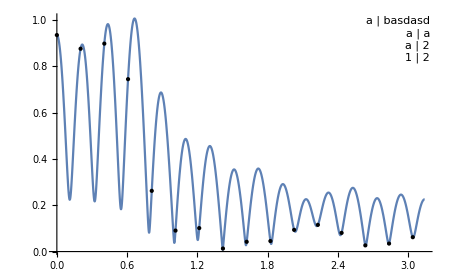

```mathematica
Plot[Abs@DTFT[[1,1]],{x,0,π},Epilog->{PointSize[Medium],Point[a]}, PlotRange->All,ImageSize->450]
```

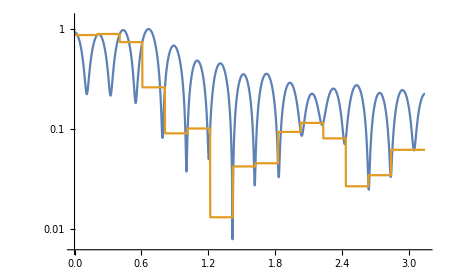

```mathematica
LogPlot[{Abs@DTFT[[1,1]],Interpolation[a,InterpolationOrder->0][x]},{x,0,π},PlotRange->All,ImageSize->450]
```

#### Testy

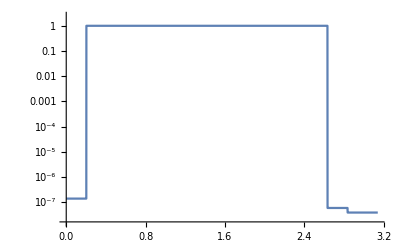
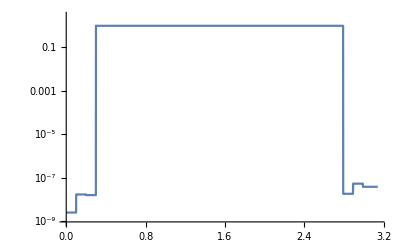
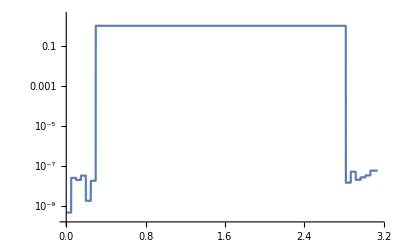
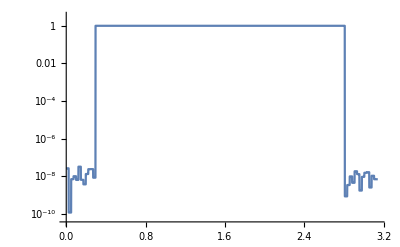
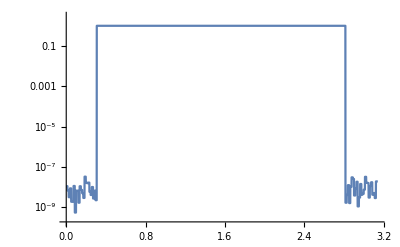
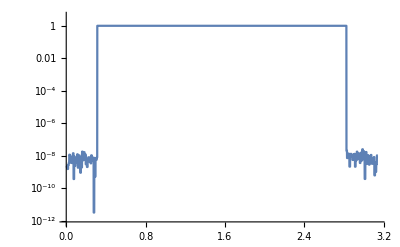

```mathematica
LogPlot[#,{x,0,π}]&/@interdDouble
```

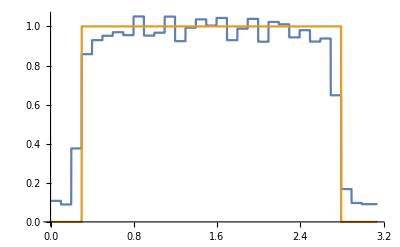

```mathematica
Plot[{interd[[2,4]],interdDouble[[2]]},{x,0,π}]
```

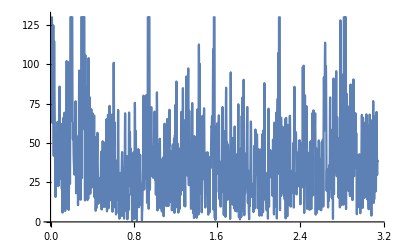

```mathematica
Plot[Abs@rotDTFT[[6,1]],{x,0,π}]
```

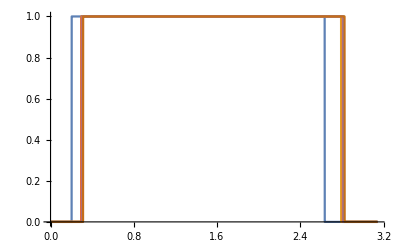

```mathematica
Plot[interdDouble,{x,0,π}]
```

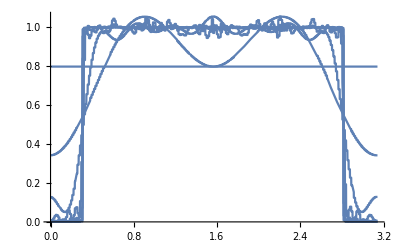

```mathematica
Plot[interd[[5,2;;8]],{x,0,π},PlotRange->Full]
```

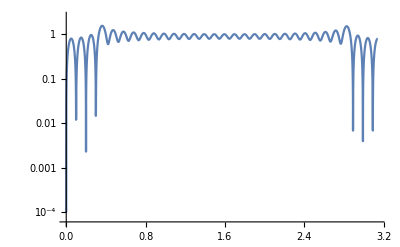
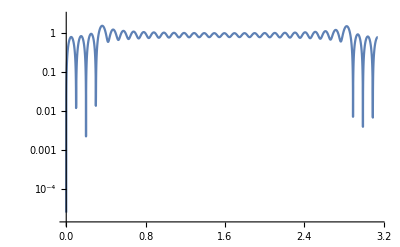

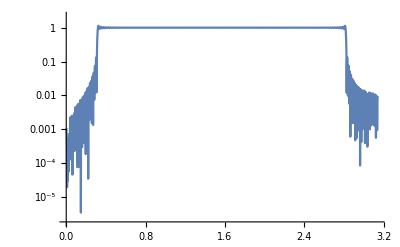
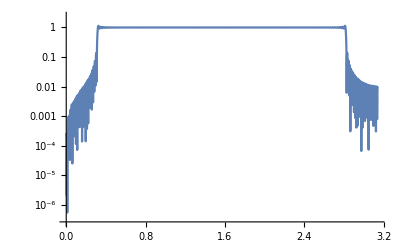

```mathematica
DTFTPlot[[2,7;;8]]
rotDTFTPlot[[5,7;;8]]
```

#### Stare

```mathematica
(*interd=Table[Interpolation[dataForInter[[i,j]],InterpolationOrder->0][x],{i,1,Length@DTFT},{j,1,Length@DTFT[[1]]}];*)
```

```mathematica
(*DTFTMeanSq =Table[NIntegrate[(Abs@DTFT[[i,j]]-interd[[i,j]])^2,{x,0,π}],{i,1,Length@DTFT},{j,1,Length@DTFT[[1]]}];
Grid@Prepend[DTFTMeanSq,bits]*)
```

```mathematica
(*rotDTFTMeanSq =Table[NIntegrate[(Abs@rotDTFT[[i,j]]-interd[[i,j]])^2,{x,0,π}],{i,1,Length@DTFT},{j,1,Length@DTFT[[1]]}];*)
```

```mathematica
(*idDTFTMeanSq =Table[NIntegrate[(Abs@DTFT[[i,j]]-interdDouble[[i]])^2,{x,0,π}],{i,1,Length@DTFT},{j,1,Length@DTFT[[1]]}];*)
```

```mathematica
leeg[xl_List,d_,points_List,numb_List,numb2_List,nam_List,args___]:=LogPlot[xl,d,
Epilog->{PointSize[Medium],Point[points],Inset[Panel[Grid[MapIndexed[{Graphics[{ColorData[1,First@#2],Thick,Line[{{0,0},{1,0}}]},AspectRatio->.1,ImageSize->20],First@nam[[#2]],First@numb[[#2]],First@numb2[[#2]]}&,xl]]],Offset[{-2,2},Scaled[{1,1}]],{Right,Top}]},args];
```

```mathematica
logDTFTs=Table[leeg[{(Abs@DTFT[[i,j]]),(Abs@rotDTFT[[i,j]])},{x,0,π},dataForInterLog[[i,j]],{DTFTMeanSq[[i,j]],rotDTFTMeanSq[[i,j]]},{idDTFTMeanSq[[i,j]],idrotDTFTMeanSq[[i,j]]},{"coefs","rotCoefs"},PlotRange->All,ImageSize->450],{i,1,Length@DTFT},{j,1,Length@DTFT[[1]]}];
```

#### Odchylenie obciętej dyskretnej i od obciącej ciągłej

```mathematica
(*TemperatureGrid[rotDTFTMeanSq]*)
```

| 0 | 2 | 4 | 6 | 8 | 10 | 12 | 14 | 16
32 | 0.076561 | 0.139887 | 0.156438 | 0.161099 | 0.161839 | 0.162125 | 0.162194 | 0.162208 | 0.162212
64 | 0.0471467 | 0.0680178 | 0.0767857 | 0.0791644 | 0.0797785 | 0.0798845 | 0.0799299 | 0.0799409 | 0.0799444
128 | 0.0242977 | 0.0325548 | 0.0369611 | 0.0382973 | 0.0385677 | 0.0386404 | 0.0386569 | 0.0386614 | 0.0386627
256 | 0.0111298 | 0.0160621 | 0.0181187 | 0.0186753 | 0.018816 | 0.0188532 | 0.0188616 | 0.018864 | 0.0188646
512 | 0.00537863 | 0.00806512 | 0.00900243 | 0.00928628 | 0.00935694 | 0.00937323 | 0.00937752 | 0.00937883 | 0.00937908
1024 | 0.00291079 | 0.00394458 | 0.00448649 | 0.00463346 | 0.00467126 | 0.00468098 | 0.00468343 | 0.00468406 | 0.00468421

```mathematica
DTFTPlot=Map[LogPlot[Abs[#],{x,0,π},PlotRange->All,PlotLegends->Automatic]&,DTFT,{2}];
rotDTFTPlot=Map[LogPlot[Abs[#],{x,0,π},PlotRange->All,PlotLegends->Automatic]&,rotDTFT,{2}];
```

## Stare Low pass

### 0.2

```mathematica
nn={32,64,128,256,512,1024};
bits=Range[0,16,2];
names=Outer["filtr"<>ToString[#1-1]<>"-"<>ToString[#2]<>".dat" &,nn,bits];
data=Map[Import[#,"Data"][[All,11]]&,names,{2}];
rotData=Map[RotateLeft[#,(Length@#+1)/2]&,data,{2}];
```

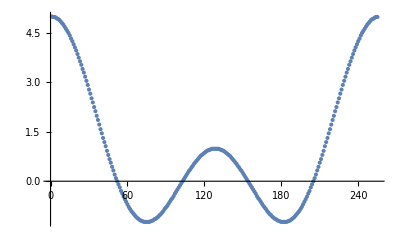

```mathematica
ListPlot@data[[4,4]]
```

```mathematica
data2=Map[Abs@Fourier[#, FourierParameters->{-1, 1}]&,data,{2}];
rotData2=Map[Abs@Fourier[#, FourierParameters->{-1, 1}]&,rotData,{2}];
dataPlot=Map[ListLogPlot[#,PlotRange->Full,Joined->True,ImageSize->450]&,data2,{2}];
Grid@Prepend[dataPlot,bits];
```

```mathematica
DTFT=Map[ListFourierSequenceTransform[#,x]/Length@(#)&,data,{2}];
rotDTFT=Map[ListFourierSequenceTransform[#,x]/Length@#&,rotData,{2}];
```

```mathematica
names2=Outer["filtr"<>ToString[#1-1]<>"-16.dat" &,nn];
dataDouble=Map[Import[#,"Data"][[All,9]]&,names2];
data2Double=Map[Abs@Fourier[#, FourierParameters->{-1, 1}]&,dataDouble,{1}];
dataForInterDouble= Map[{Table[i,{i,0,1-1/(Length@#),2/(Length@#)}]π,#[[1;;(Length@#+1)/2]]}ᵀ &,data2Double];
interdDouble=Table[Interpolation[dataForInterDouble[[i]],InterpolationOrder->0][x],{i,1,Length@DTFT}];
```

```mathematica
LogPlot[#,{x,0,π}]&/@interdDouble;
```

```mathematica
dataForInter= Map[{Table[i,{i,0,1-1/(Length@#),2/(Length@#)}]π,#[[1;;(Length@#+1)/2]]}ᵀ &,data2,{2}];
dataForInterLog= Map[{Table[i,{i,0,1-1/(Length@#),2/(Length@#)}]π,Log@#[[1;;(Length@#+1)/2]]}ᵀ &,data2,{2}];
```

```mathematica
DTFTPlot=Map[LogPlot[Abs[#],{x,0,π},PlotRange->All,PlotLegends->Automatic]&,DTFT,{2}];
rotDTFTPlot=Map[LogPlot[Abs[#]/Length@#,{x,0,π},PlotRange->All,PlotLegends->Automatic]&,rotDTFT,{2}];
```

```mathematica
leeg[xl_List,d_,points_List,numb_List,numb2_List,nam_List,args___]:=LogPlot[xl,d,
Epilog->{PointSize[Medium],Point[points],Inset[Panel[Grid[MapIndexed[{Graphics[{ColorData[1,First@#2],Thick,Line[{{0,0},{1,0}}]},AspectRatio->.1,ImageSize->20],First@nam[[#2]],First@numb[[#2]],First@numb2[[#2]]}&,xl]]],Offset[{-2,2},Scaled[{1,1}]],{Right,Top}]},args];
```

```mathematica
interd=Table[Interpolation[dataForInter[[i,j]],InterpolationOrder->0][x],{i,1,Length@DTFT},{j,1,Length@DTFT[[1]]}];
```

```mathematica
DTFTMeanSq =Table[NIntegrate[(Abs@DTFT[[i,j]]-interd[[i,j]])^2,{x,0,π}],{i,1,Length@DTFT},{j,1,Length@DTFT[[1]]}];
Grid@Prepend[DTFTMeanSq,bits]
```

0 | 2 | 4 | 6 | 8 | 10 | 12 | 14 | 16
0.23518 | 0.415428 | 0.467573 | 0.479466 | 0.481376 | 0.482122 | 0.482304 | 0.48234 | 0.482355
0.284306 | 0.363889 | 0.393089 | 0.400613 | 0.402466 | 0.402831 | 0.402955 | 0.402988 | 0.402997
0.284012 | 0.334173 | 0.352531 | 0.356381 | 0.35738 | 0.35765 | 0.357713 | 0.357731 | 0.357735
0.295502 | 0.329305 | 0.339383 | 0.341864 | 0.342521 | 0.34268 | 0.342719 | 0.34273 | 0.342732
0.307597 | 0.326188 | 0.331469 | 0.332916 | 0.33329 | 0.33339 | 0.333418 | 0.333424 | 0.333425
0.309099 | 0.320332 | 0.324062 | 0.32496 | 0.325198 | 0.32526 | 0.325274 | 0.325278 | 0.325279

```mathematica
rotDTFTMeanSq =Table[NIntegrate[(Abs@rotDTFT[[i,j]]-interd[[i,j]])^2,{x,0,π}],{i,1,Length@DTFT},{j,1,Length@DTFT[[1]]}];
Grid@Prepend[rotDTFTMeanSq,bits]
```

0 | 2 | 4 | 6 | 8 | 10 | 12 | 14 | 16
0.0233781 | 0.0618018 | 0.0755535 | 0.0794187 | 0.080019 | 0.0802984 | 0.080354 | 0.0803672 | 0.0803719
0.0156977 | 0.0310591 | 0.0371427 | 0.0382571 | 0.038642 | 0.0387176 | 0.0387494 | 0.0387566 | 0.0387587
0.00788651 | 0.0146943 | 0.0179764 | 0.0187422 | 0.0189491 | 0.0190012 | 0.0190135 | 0.019017 | 0.019018
0.0039049 | 0.00735694 | 0.00886565 | 0.00926766 | 0.00938064 | 0.00940765 | 0.00941413 | 0.00941582 | 0.00941624
0.00189039 | 0.00372534 | 0.00441772 | 0.00461613 | 0.00466842 | 0.00468134 | 0.00468448 | 0.00468538 | 0.00468558
0.000962019 | 0.00182557 | 0.00221764 | 0.00230455 | 0.00232886 | 0.00233517 | 0.00233676 | 0.00233717 | 0.00233727

```mathematica
idDTFTMeanSq =Table[NIntegrate[(Abs@DTFT[[i,j]]-interdDouble[[i]])^2,{x,0,π}],{i,1,Length@DTFT},{j,1,Length@DTFT[[1]]}];
idrotDTFTMeanSq =Table[NIntegrate[(Abs@rotDTFT[[i,j]]-interdDouble[[i]])^2,{x,0,π}],{i,1,Length@DTFT},{j,1,Length@DTFT[[1]]}];
Grid@Prepend[idDTFTMeanSq,bits]
Grid@Prepend[idrotDTFTMeanSq,bits]
```

0 | 2 | 4 | 6 | 8 | 10 | 12 | 14 | 16
0.405553 | 0.454447 | 0.477975 | 0.481527 | 0.48203 | 0.482296 | 0.482342 | 0.482352 | 0.482357
0.367345 | 0.389886 | 0.399651 | 0.402178 | 0.40288 | 0.402951 | 0.402985 | 0.402996 | 0.402999
0.336255 | 0.350347 | 0.356289 | 0.357384 | 0.357623 | 0.35771 | 0.357731 | 0.357735 | 0.357736
0.327623 | 0.338187 | 0.341669 | 0.342462 | 0.342671 | 0.342715 | 0.342728 | 0.342732 | 0.342733
0.323112 | 0.331301 | 0.332747 | 0.33327 | 0.33338 | 0.333415 | 0.333423 | 0.333425 | 0.333426
0.319616 | 0.323385 | 0.324889 | 0.325183 | 0.325254 | 0.325273 | 0.325278 | 0.325279 | 0.325279

0 | 2 | 4 | 6 | 8 | 10 | 12 | 14 | 16
0.0802243 | 0.0694843 | 0.0787397 | 0.0801102 | 0.0802283 | 0.0803527 | 0.0803649 | 0.0803703 | 0.0803724
0.0372886 | 0.0353129 | 0.0382651 | 0.0385084 | 0.0387315 | 0.0387453 | 0.038756 | 0.0387584 | 0.0387591
0.018164 | 0.0175248 | 0.0186967 | 0.0189132 | 0.0189849 | 0.0190106 | 0.0190167 | 0.0190177 | 0.0190181
0.00887397 | 0.00857783 | 0.00917145 | 0.00935112 | 0.00940097 | 0.00941207 | 0.00941533 | 0.00941608 | 0.0094163
0.00408537 | 0.00435367 | 0.00455777 | 0.00465373 | 0.00467672 | 0.0046837 | 0.00468509 | 0.00468553 | 0.00468562
0.00214296 | 0.00207797 | 0.00228295 | 0.00232135 | 0.00233301 | 0.00233628 | 0.00233703 | 0.00233723 | 0.00233728

```mathematica
logDTFTs=Table[leeg[{(Abs@DTFT[[i,j]]),(Abs@rotDTFT[[i,j]])},{x,0,π},dataForInterLog[[i,j]],{DTFTMeanSq[[i,j]],rotDTFTMeanSq[[i,j]]},{idDTFTMeanSq[[i,j]],idrotDTFTMeanSq[[i,j]]},{"coefs","rotCoefs"},PlotRange->All,ImageSize->450],{i,1,Length@DTFT},{j,1,Length@DTFT[[1]]}];
```

```mathematica
Export["plots.png",Grid@logDTFTs];
```

### 0.02

```mathematica
nn={32,64,128,256,512,1024};
bits=Range[0,16,2];
names=Outer["filtr"<>ToString[#1-1]<>"-"<>ToString[#2]<>".dat" &,nn,bits];
data=Map[Import[#,"Data"][[All,11]]&,names,{2}];
rotData=Map[RotateLeft[#,(Length@#+1)/2]&,data,{2}];
```

```mathematica
data2=Map[Abs@Fourier[#, FourierParameters->{-1, 1}]&,data,{2}];
rotData2=Map[Abs@Fourier[#, FourierParameters->{-1, 1}]&,rotData,{2}];
dataPlot=Map[ListLogPlot[#,PlotRange->Full,Joined->True,ImageSize->450]&,data2,{2}];
Grid@Prepend[dataPlot,bits];
```

```mathematica
DTFT=Map[ListFourierSequenceTransform[#,x]/Length@(#)&,data,{2}];
rotDTFT=Map[ListFourierSequenceTransform[#,x]/Length@#&,rotData,{2}];
```

```mathematica
names2=Outer["filtr"<>ToString[#1-1]<>"-16.dat" &,nn];
dataDouble=Map[Import[#,"Data"][[All,9]]&,names2];
data2Double=Map[Abs@Fourier[#, FourierParameters->{-1, 1}]&,dataDouble,{1}];
dataForInterDouble= Map[{Table[i,{i,0,1-1/(Length@#),2/(Length@#)}]π,#[[1;;(Length@#+1)/2]]}ᵀ &,data2Double];
interdDouble=Table[Interpolation[dataForInterDouble[[i]],InterpolationOrder->0][x],{i,1,Length@DTFT}];
```

```mathematica
LogPlot[#,{x,0,π}]&/@interdDouble;
```

```mathematica
dataForInter= Map[{Table[i,{i,0,1-1/(Length@#),2/(Length@#)}]π,#[[1;;(Length@#+1)/2]]}ᵀ &,data2,{2}];
dataForInterLog= Map[{Table[i,{i,0,1-1/(Length@#),2/(Length@#)}]π,Log@#[[1;;(Length@#+1)/2]]}ᵀ &,data2,{2}];
```

```mathematica
DTFTPlot=Map[LogPlot[Abs[#],{x,0,π},PlotRange->All,PlotLegends->Automatic]&,DTFT,{2}];
rotDTFTPlot=Map[LogPlot[Abs[#]/Length@#,{x,0,π},PlotRange->All,PlotLegends->Automatic]&,rotDTFT,{2}];
```

```mathematica
leeg[xl_List,d_,points_List,numb_List,numb2_List,nam_List,args___]:=LogPlot[xl,d,
Epilog->{PointSize[Medium],Point[points],Inset[Panel[Grid[MapIndexed[{Graphics[{ColorData[1,First@#2],Thick,Line[{{0,0},{1,0}}]},AspectRatio->.1,ImageSize->20],First@nam[[#2]],First@numb[[#2]],First@numb2[[#2]]}&,xl]]],Offset[{-2,2},Scaled[{1,1}]],{Right,Top}]},args];
```

```mathematica
interd=Table[Interpolation[dataForInter[[i,j]],InterpolationOrder->0][x],{i,1,Length@DTFT},{j,1,Length@DTFT[[1]]}];
```

```mathematica
DTFTMeanSq =Table[NIntegrate[(Abs@DTFT[[i,j]]-interd[[i,j]])^2,{x,0,π}],{i,1,Length@DTFT},{j,1,Length@DTFT[[1]]}];
Grid@Prepend[DTFTMeanSq,bits]
```

0 | 2 | 4 | 6 | 8 | 10 | 12 | 14 | 16
0.23518 | 0.415428 | 0.467573 | 0.479466 | 0.481376 | 0.482122 | 0.482304 | 0.48234 | 0.482355
0.284306 | 0.363889 | 0.393089 | 0.400613 | 0.402466 | 0.402831 | 0.402955 | 0.402988 | 0.402997
0.284012 | 0.334173 | 0.352531 | 0.356381 | 0.35738 | 0.35765 | 0.357713 | 0.357731 | 0.357735
0.295502 | 0.329305 | 0.339383 | 0.341864 | 0.342521 | 0.34268 | 0.342719 | 0.34273 | 0.342732
0.307597 | 0.326188 | 0.331469 | 0.332916 | 0.33329 | 0.33339 | 0.333418 | 0.333424 | 0.333425
0.309099 | 0.320332 | 0.324062 | 0.32496 | 0.325198 | 0.32526 | 0.325274 | 0.325278 | 0.325279

```mathematica
rotDTFTMeanSq =Table[NIntegrate[(Abs@rotDTFT[[i,j]]-interd[[i,j]])^2,{x,0,π}],{i,1,Length@DTFT},{j,1,Length@DTFT[[1]]}];
Grid@Prepend[rotDTFTMeanSq,bits]
```

0 | 2 | 4 | 6 | 8 | 10 | 12 | 14 | 16
0.0233781 | 0.0618018 | 0.0755535 | 0.0794187 | 0.080019 | 0.0802984 | 0.080354 | 0.0803672 | 0.0803719
0.0156977 | 0.0310591 | 0.0371427 | 0.0382571 | 0.038642 | 0.0387176 | 0.0387494 | 0.0387566 | 0.0387587
0.00788651 | 0.0146943 | 0.0179764 | 0.0187422 | 0.0189491 | 0.0190012 | 0.0190135 | 0.019017 | 0.019018
0.0039049 | 0.00735694 | 0.00886565 | 0.00926766 | 0.00938064 | 0.00940765 | 0.00941413 | 0.00941582 | 0.00941624
0.00189039 | 0.00372534 | 0.00441772 | 0.00461613 | 0.00466842 | 0.00468134 | 0.00468448 | 0.00468538 | 0.00468558
0.000962019 | 0.00182557 | 0.00221764 | 0.00230455 | 0.00232886 | 0.00233517 | 0.00233676 | 0.00233717 | 0.00233727

```mathematica
idDTFTMeanSq =Table[NIntegrate[(Abs@DTFT[[i,j]]-interdDouble[[i]])^2,{x,0,π}],{i,1,Length@DTFT},{j,1,Length@DTFT[[1]]}];
idrotDTFTMeanSq =Table[NIntegrate[(Abs@rotDTFT[[i,j]]-interdDouble[[i]])^2,{x,0,π}],{i,1,Length@DTFT},{j,1,Length@DTFT[[1]]}];
Grid@Prepend[idDTFTMeanSq,bits]
Grid@Prepend[idrotDTFTMeanSq,bits]
```

0 | 2 | 4 | 6 | 8 | 10 | 12 | 14 | 16
0.405553 | 0.454447 | 0.477975 | 0.481527 | 0.48203 | 0.482296 | 0.482342 | 0.482352 | 0.482357
0.367345 | 0.389886 | 0.399651 | 0.402178 | 0.40288 | 0.402951 | 0.402985 | 0.402996 | 0.402999
0.336255 | 0.350347 | 0.356289 | 0.357384 | 0.357623 | 0.35771 | 0.357731 | 0.357735 | 0.357736
0.327623 | 0.338187 | 0.341669 | 0.342462 | 0.342671 | 0.342715 | 0.342728 | 0.342732 | 0.342733
0.323112 | 0.331301 | 0.332747 | 0.33327 | 0.33338 | 0.333415 | 0.333423 | 0.333425 | 0.333426
0.319616 | 0.323385 | 0.324889 | 0.325183 | 0.325254 | 0.325273 | 0.325278 | 0.325279 | 0.325279

0 | 2 | 4 | 6 | 8 | 10 | 12 | 14 | 16
0.0802243 | 0.0694843 | 0.0787397 | 0.0801102 | 0.0802283 | 0.0803527 | 0.0803649 | 0.0803703 | 0.0803724
0.0372886 | 0.0353129 | 0.0382651 | 0.0385084 | 0.0387315 | 0.0387453 | 0.038756 | 0.0387584 | 0.0387591
0.018164 | 0.0175248 | 0.0186967 | 0.0189132 | 0.0189849 | 0.0190106 | 0.0190167 | 0.0190177 | 0.0190181
0.00887397 | 0.00857783 | 0.00917145 | 0.00935112 | 0.00940097 | 0.00941207 | 0.00941533 | 0.00941608 | 0.0094163
0.00408537 | 0.00435367 | 0.00455777 | 0.00465373 | 0.00467672 | 0.0046837 | 0.00468509 | 0.00468553 | 0.00468562
0.00214296 | 0.00207797 | 0.00228295 | 0.00232135 | 0.00233301 | 0.00233628 | 0.00233703 | 0.00233723 | 0.00233728

```mathematica
logDTFTs=Table[leeg[{(Abs@DTFT[[i,j]]),(Abs@rotDTFT[[i,j]])},{x,0,π},dataForInterLog[[i,j]],{DTFTMeanSq[[i,j]],rotDTFTMeanSq[[i,j]]},{idDTFTMeanSq[[i,j]],idrotDTFTMeanSq[[i,j]]},{"coefs","rotCoefs"},PlotRange->All,ImageSize->450],{i,1,Length@DTFT},{j,1,Length@DTFT[[1]]}];
```

```mathematica
Export["plots.png",Grid@logDTFTs];
```

## Stare High pass

### 0.2

```mathematica
nn={32,64,128,256,512,1024};
bits=Range[0,16,2];
names=Outer["filtr"<>ToString[#1-1]<>"h-"<>ToString[#2]<>".dat" &,nn,bits];
data=Map[Import[#,"Data"][[All,11]]&,names,{2}];
rotData=Map[RotateLeft[#,(Length@#+1)/2]&,data,{2}];
```

```mathematica
data2=Map[Abs@Fourier[#, FourierParameters->{-1, 1}]&,data,{2}];
rotData2=Map[Abs@Fourier[#, FourierParameters->{-1, 1}]&,rotData,{2}];
dataPlot=Map[ListLogPlot[#,PlotRange->Full,Joined->True,ImageSize->450]&,data2,{2}];
Grid@Prepend[dataPlot,bits];
```

```mathematica
DTFT=Map[ListFourierSequenceTransform[#,x]/Length@(#)&,data,{2}];
rotDTFT=Map[ListFourierSequenceTransform[#,x]/Length@#&,rotData,{2}];
```

```mathematica
names2=Outer["filtr"<>ToString[#1-1]<>"h-16.dat" &,nn];
dataDouble=Map[Import[#,"Data"][[All,9]]&,names2];
data2Double=Map[Abs@Fourier[#, FourierParameters->{-1, 1}]&,dataDouble,{1}];
dataForInterDouble= Map[{Table[i,{i,0,1-1/(Length@#),2/(Length@#)}]π,#[[1;;(Length@#+1)/2]]}ᵀ &,data2Double];
interdDouble=Table[Interpolation[dataForInterDouble[[i]],InterpolationOrder->0][x],{i,1,Length@DTFT}];
```

```mathematica
LogPlot[#,{x,0,π}]&/@interdDouble;
```

```mathematica
dataForInter= Map[{Table[i,{i,0,1-1/(Length@#),2/(Length@#)}]π,#[[1;;(Length@#+1)/2]]}ᵀ &,data2,{2}];
dataForInterLog= Map[{Table[i,{i,0,1-1/(Length@#),2/(Length@#)}]π,Log@#[[1;;(Length@#+1)/2]]}ᵀ &,data2,{2}];
```

```mathematica
DTFTPlot=Map[LogPlot[Abs[#],{x,0,π},PlotRange->All,PlotLegends->Automatic]&,DTFT,{2}];
rotDTFTPlot=Map[LogPlot[Abs[#]/Length@#,{x,0,π},PlotRange->All,PlotLegends->Automatic]&,rotDTFT,{2}];
```

```mathematica
leeg[xl_List,d_,points_List,numb_List,numb2_List,nam_List,args___]:=LogPlot[xl,d,
Epilog->{PointSize[Medium],Point[points],Inset[Panel[Grid[MapIndexed[{Graphics[{ColorData[1,First@#2],Thick,Line[{{0,0},{1,0}}]},AspectRatio->.1,ImageSize->20],First@nam[[#2]],First@numb[[#2]],First@numb2[[#2]]}&,xl]]],Offset[{-2,2},Scaled[{1,1}]],{Right,Top}]},args];
```

```mathematica
interd=Table[Interpolation[dataForInter[[i,j]],InterpolationOrder->0][x],{i,1,Length@DTFT},{j,1,Length@DTFT[[1]]}];
```

```mathematica
DTFTMeanSq =Table[NIntegrate[(Abs@DTFT[[i,j]]-interd[[i,j]])^2,{x,0,π}],{i,1,Length@DTFT},{j,1,Length@DTFT[[1]]}];
Grid@Prepend[DTFTMeanSq,bits]
```

0 | 2 | 4 | 6 | 8 | 10 | 12 | 14 | 16
0.223024 | 0.29682 | 0.317848 | 0.32049 | 0.320925 | 0.321072 | 0.321114 | 0.321122 | 0.321127
0.285114 | 0.311868 | 0.322632 | 0.326517 | 0.327322 | 0.32745 | 0.327486 | 0.327499 | 0.327503
0.304456 | 0.324962 | 0.333422 | 0.335053 | 0.335418 | 0.33553 | 0.335557 | 0.335563 | 0.335564
0.326496 | 0.345777 | 0.350994 | 0.35241 | 0.352717 | 0.352785 | 0.352803 | 0.352808 | 0.352809
0.350791 | 0.359342 | 0.361946 | 0.3627 | 0.362872 | 0.362926 | 0.362939 | 0.362942 | 0.362943
0.35715 | 0.363383 | 0.365519 | 0.36604 | 0.366151 | 0.366186 | 0.366193 | 0.366195 | 0.366196

```mathematica
rotDTFTMeanSq =Table[NIntegrate[(Abs@rotDTFT[[i,j]]-interd[[i,j]])^2,{x,0,π}],{i,1,Length@DTFT},{j,1,Length@DTFT[[1]]}];
Grid@Prepend[rotDTFTMeanSq,bits]
```

0 | 2 | 4 | 6 | 8 | 10 | 12 | 14 | 16
0.0276746 | 0.0616771 | 0.0760925 | 0.0794739 | 0.0800259 | 0.0803025 | 0.0803531 | 0.0803672 | 0.0803719
0.0189623 | 0.0314241 | 0.0372295 | 0.0382546 | 0.0386535 | 0.0387193 | 0.0387492 | 0.0387566 | 0.0387587
0.00873955 | 0.0144921 | 0.0179689 | 0.0187293 | 0.018943 | 0.0190002 | 0.0190138 | 0.019017 | 0.019018
0.00411645 | 0.00711421 | 0.00880487 | 0.00924424 | 0.00937661 | 0.00940612 | 0.00941376 | 0.00941573 | 0.00941621
0.00207812 | 0.00365134 | 0.00437823 | 0.00460702 | 0.00466606 | 0.00468081 | 0.00468433 | 0.00468535 | 0.00468557
0.0010712 | 0.00178402 | 0.00220307 | 0.00229896 | 0.00232747 | 0.00233477 | 0.00233666 | 0.00233715 | 0.00233726

```mathematica
idDTFTMeanSq =Table[NIntegrate[(Abs@DTFT[[i,j]]-interdDouble[[i]])^2,{x,0,π}],{i,1,Length@DTFT},{j,1,Length@DTFT[[1]]}];
idrotDTFTMeanSq =Table[NIntegrate[(Abs@rotDTFT[[i,j]]-interdDouble[[i]])^2,{x,0,π}],{i,1,Length@DTFT},{j,1,Length@DTFT[[1]]}];
Grid@Prepend[idDTFTMeanSq,bits]
Grid@Prepend[idrotDTFTMeanSq,bits]
```

0 | 2 | 4 | 6 | 8 | 10 | 12 | 14 | 16
0.323377 | 0.321491 | 0.320743 | 0.320985 | 0.321115 | 0.321116 | 0.321127 | 0.321127 | 0.321128
0.326602 | 0.325357 | 0.326692 | 0.327382 | 0.327461 | 0.327494 | 0.327501 | 0.327503 | 0.327504
0.331299 | 0.33307 | 0.335041 | 0.33541 | 0.335535 | 0.335557 | 0.335562 | 0.335564 | 0.335565
0.348133 | 0.351178 | 0.352341 | 0.352714 | 0.352783 | 0.352804 | 0.352808 | 0.352809 | 0.352809
0.362607 | 0.362268 | 0.362864 | 0.362899 | 0.362929 | 0.362939 | 0.362943 | 0.362943 | 0.362943
0.364627 | 0.365842 | 0.36607 | 0.366164 | 0.366187 | 0.366195 | 0.366196 | 0.366196 | 0.366196

0 | 2 | 4 | 6 | 8 | 10 | 12 | 14 | 16
0.0802244 | 0.0694843 | 0.0787397 | 0.0801102 | 0.0802283 | 0.0803527 | 0.0803649 | 0.0803703 | 0.0803724
0.0373397 | 0.0355155 | 0.0383278 | 0.0385249 | 0.0387357 | 0.0387464 | 0.0387563 | 0.0387585 | 0.0387591
0.018164 | 0.0175248 | 0.0186967 | 0.0189132 | 0.0189849 | 0.0190106 | 0.0190167 | 0.0190177 | 0.0190181
0.00868072 | 0.00849328 | 0.00914804 | 0.00934512 | 0.00939947 | 0.0094117 | 0.00941524 | 0.00941606 | 0.0094163
0.00408537 | 0.00435367 | 0.00455777 | 0.00465373 | 0.00467672 | 0.0046837 | 0.00468509 | 0.00468553 | 0.00468562
0.00214296 | 0.00207797 | 0.00228295 | 0.00232135 | 0.00233301 | 0.00233628 | 0.00233703 | 0.00233723 | 0.00233728

```mathematica
logDTFTs=Table[leeg[{(Abs@DTFT[[i,j]]),(Abs@rotDTFT[[i,j]])},{x,0,π},dataForInterLog[[i,j]],{DTFTMeanSq[[i,j]],rotDTFTMeanSq[[i,j]]},{idDTFTMeanSq[[i,j]],idrotDTFTMeanSq[[i,j]]},{"coefs","rotCoefs"},PlotRange->All,ImageSize->450],{i,1,Length@DTFT},{j,1,Length@DTFT[[1]]}];
```

```mathematica
Export["plots-highpass.png",Grid@Prepend[logDTFTs,bits]];
```

### 0.4

## Tests

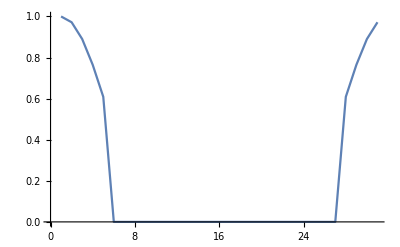

```mathematica
ListLinePlot@Import["filtr31-16.dat","Data"][[All,1]]
```

N@